```mathematica
f[k_,w_]:=Return[
data=sheet[[k]];
{ii,jj}=data//Dimensions;
GeneList=Take[data,{2,ii},{Position [data,"GENES"][[1,2]]}]//Flatten;(*GENES*)
TickList=Table[{i,GeneList[[i]]},{i,1,ii-1}];
CatList=Take[data,{2,ii},{Position [data,"GENES"][[1,2]]+1}]//Flatten;(*GENES (+1) collumn = KO *)
TickListCat=Table[{i,CatList[[i]]},{i,1,ii-1}];
PlotA=ArrayPlot[Take[data,{2,ii},{Position [data,"GENES"][[1,2]]+9,jj-6}], ImageSize ->w,PlotRange->{-7,7},ColorFunction->(Blend[{Green,White,Red},#]&),ColorFunctionScaling->True,Mesh->True,PlotLabel->"Log_2 fold changes of probes\n["<>data[[1,Position [data,"GENES"][[1,2]]-1]]<>"; n = "<>ToString[ii-1]<>"]\n",Frame->True,FrameTicks->{{TickListCat,TickList},{None,{{1,Subscript[LL, 3]/Subscript[DD, 3]},{2,Subscript[Diel, 3]/Subscript[LL, 3]},{3,Subscript[DD, 3]/Subscript[Diel, 3]},{4,Subscript[LL, 6]/Subscript[DD, 6]},{5,Subscript[Diel, 6]/Subscript[LL, 6]},{6,Subscript[DD, 6]/Subscript[Diel, 6]}}}}]]
g[k_,w_]:=Return[
data=sheet[[k]];
{ii,jj}=data//Dimensions;
GeneList=Take[data,{2,ii},{Position [data,"GENES"][[1,2]]}]//Flatten;
TickList=Table[{i,GeneList[[i]]},{i,1,ii-1}];
CatList=Take[data,{2,ii},{Position [data,"GENES"][[1,2]]+1}]//Flatten;
TickListCat=Table[{i,CatList[[i]]},{i,1,ii-1}];
PlotB=ArrayPlot[Take[data,{2,ii},{Position [data,"GENES"][[1,2]]+3,jj-12}],ImageSize ->w,PlotRange->{-20,-3},ColorFunction->(Blend[{Cyan,White,Magenta},#] &),ColorFunctionScaling->True,Mesh->True,PlotLabel->"Log_2 normalized probes\n["<>data[[1,Position [data,"GENES"][[1,2]]-1]]<>"; n = "<>ToString[ii-1]<>"]\n",Frame->True,FrameTicks->{{TickListCat,TickList},{None,{{1,Subscript[DD, 3]},{2,Subscript[LL, 3]},{3,Subscript[Diel, 3]},{4,Subscript[DD, 6]},{5,Subscript[LL, 6]},{6,Subscript[Diel, 6]}}}}]]
p[k_,w_]:=Return[
data=sheet[[k]];
{ii,jj}=data//Dimensions;
GeneList=Take[data,{2,ii},{Position [data,"GENES"][[1,2]]}]//Flatten;(*GENES*)
TickList=Table[{i,GeneList[[i]]},{i,1,ii-1}];
CatList=Take[data,{2,ii},{Position [data,"GENES"][[1,2]]-1}]//Flatten;(*GENES (+1) collumn = KO *)
TickListCat=Table[{i,CatList[[i]]},{i,1,ii-1}];
PlotA=ArrayPlot[Take[data,{2,ii},{Position [data,"GENES"][[1,2]]+9,jj-6}], ImageSize ->w,PlotRange->{-7,7},ColorFunction->(Blend[{Green,White,Red},#]&),ColorFunctionScaling->True,Mesh->True,PlotLabel->"Log_2 fold changes of probes\n["<>data[[1,Position [data,"GENES"][[1,2]]-1]]<>"; n = "<>ToString[ii-1]<>"]\n",Frame->True,FrameTicks->{{TickListCat,TickList},{None,{{1,Subscript[LL, 3]/Subscript[DD, 3]},{2,Subscript[Diel, 3]/Subscript[LL, 3]},{3,Subscript[DD, 3]/Subscript[Diel, 3]},{4,Subscript[LL, 6]/Subscript[DD, 6]},{5,Subscript[Diel, 6]/Subscript[LL, 6]},{6,Subscript[DD, 6]/Subscript[Diel, 6]}}}}]]
q[k_,w_]:=Return[
data=sheet[[k]];
{ii,jj}=data//Dimensions;
GeneList=Take[data,{2,ii},{Position [data,"GENES"][[1,2]]}]//Flatten;
TickList=Table[{i,GeneList[[i]]},{i,1,ii-1}];
CatList=Take[data,{2,ii},{Position [data,"GENES"][[1,2]]-1}]//Flatten;
TickListCat=Table[{i,CatList[[i]]},{i,1,ii-1}];
PlotB=ArrayPlot[Take[data,{2,ii},{Position [data,"GENES"][[1,2]]+3,jj-12}],ImageSize ->w,PlotRange->{-20,-3},ColorFunction->(Blend[{Cyan,White,Magenta},#] &),ColorFunctionScaling->True,Mesh->True,PlotLabel->"Log_2 normalized probes\n["<>data[[1,Position [data,"GENES"][[1,2]]-1]]<>"; n = "<>ToString[ii-1]<>"]\n",Frame->True,FrameTicks->{{TickListCat,TickList},{None,{{1,Subscript[DD, 3]},{2,Subscript[LL, 3]},{3,Subscript[Diel, 3]},{4,Subscript[DD, 6]},{5,Subscript[LL, 6]},{6,Subscript[Diel, 6]}}}}]]
DensityPlotA=DensityPlot[x,{x,-7,7},{y,0,0.21/13.},AspectRatio-> .1,ImageSize ->{150,150},ColorFunction->(Blend[{Green,White,Red},#]&),ColorFunctionScaling->True,FrameTicks-> {{None,None},{Automatic,None}},PlotLabel->"Log_2 fold change"];
DensityPlotB=DensityPlot[x,{x,-20,-3},{y,0,0.21/13.},AspectRatio-> .1,ImageSize ->{150,150},ColorFunction->(Blend[{Cyan,White,Magenta},#] &),ColorFunctionScaling->True,FrameTicks-> {{None,None},{Automatic,None}},PlotLabel->"Log_2 probe abundance"];

sheet=Import["C:\\Users\\marin\\OneDrive\\문서\\IMCC1322_RNA-seq Figs\\RNA_seq_DEG_2\\deg_2_ver3\\Carbohydrate_metabolism.xlsx","XLSX"];
m=Dimensions[sheet][[1]]
 DensityPlotA;
SlideView[Table[f[j,1400],{j,2,m}]];
DensityPlotB;
SlideView[Table[g[j,1400],{j,2,m}]];
```

16

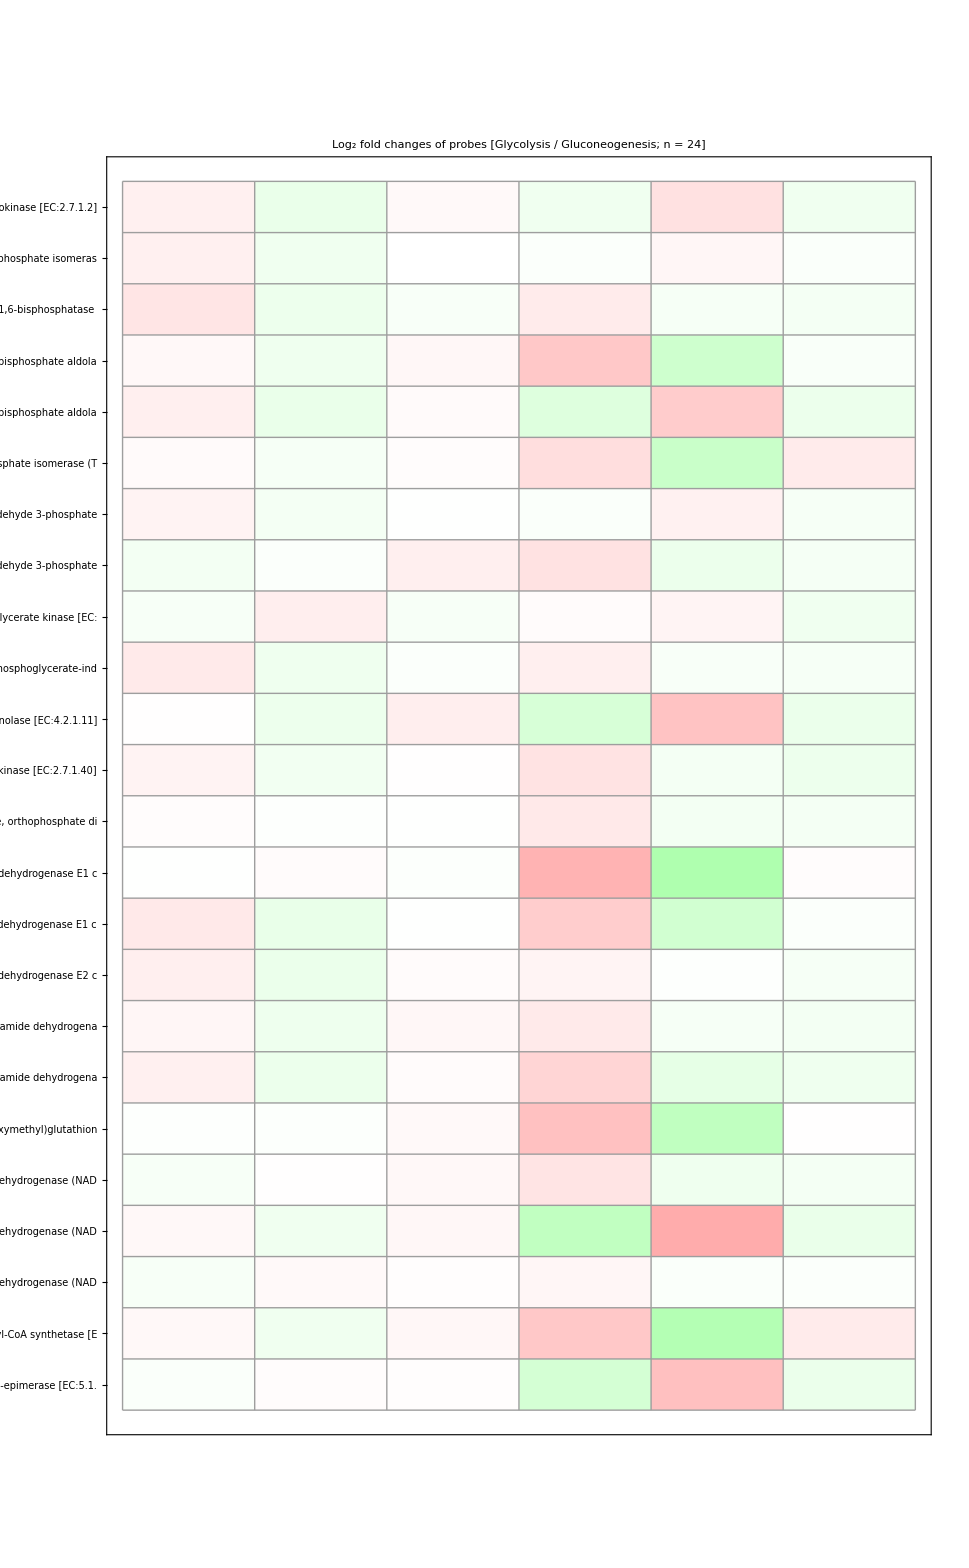

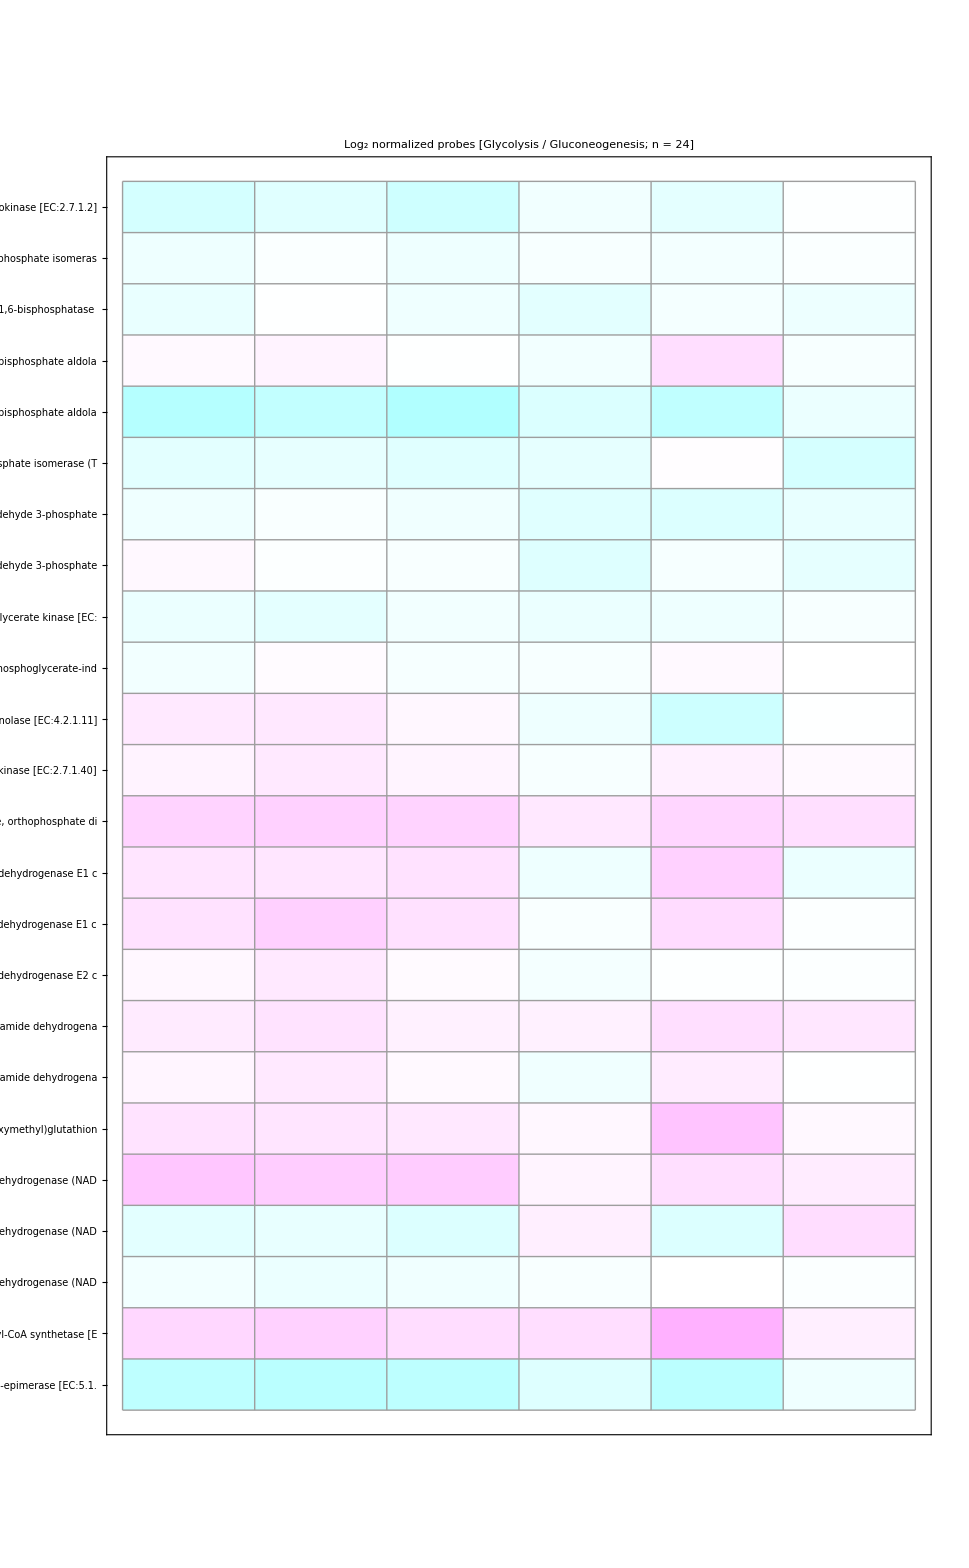

```mathematica
Graphics[{Inset[Show[f[2,970],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{.1,.65}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[2,970],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{.1,.65}]]},AspectRatio->Automatic]
```

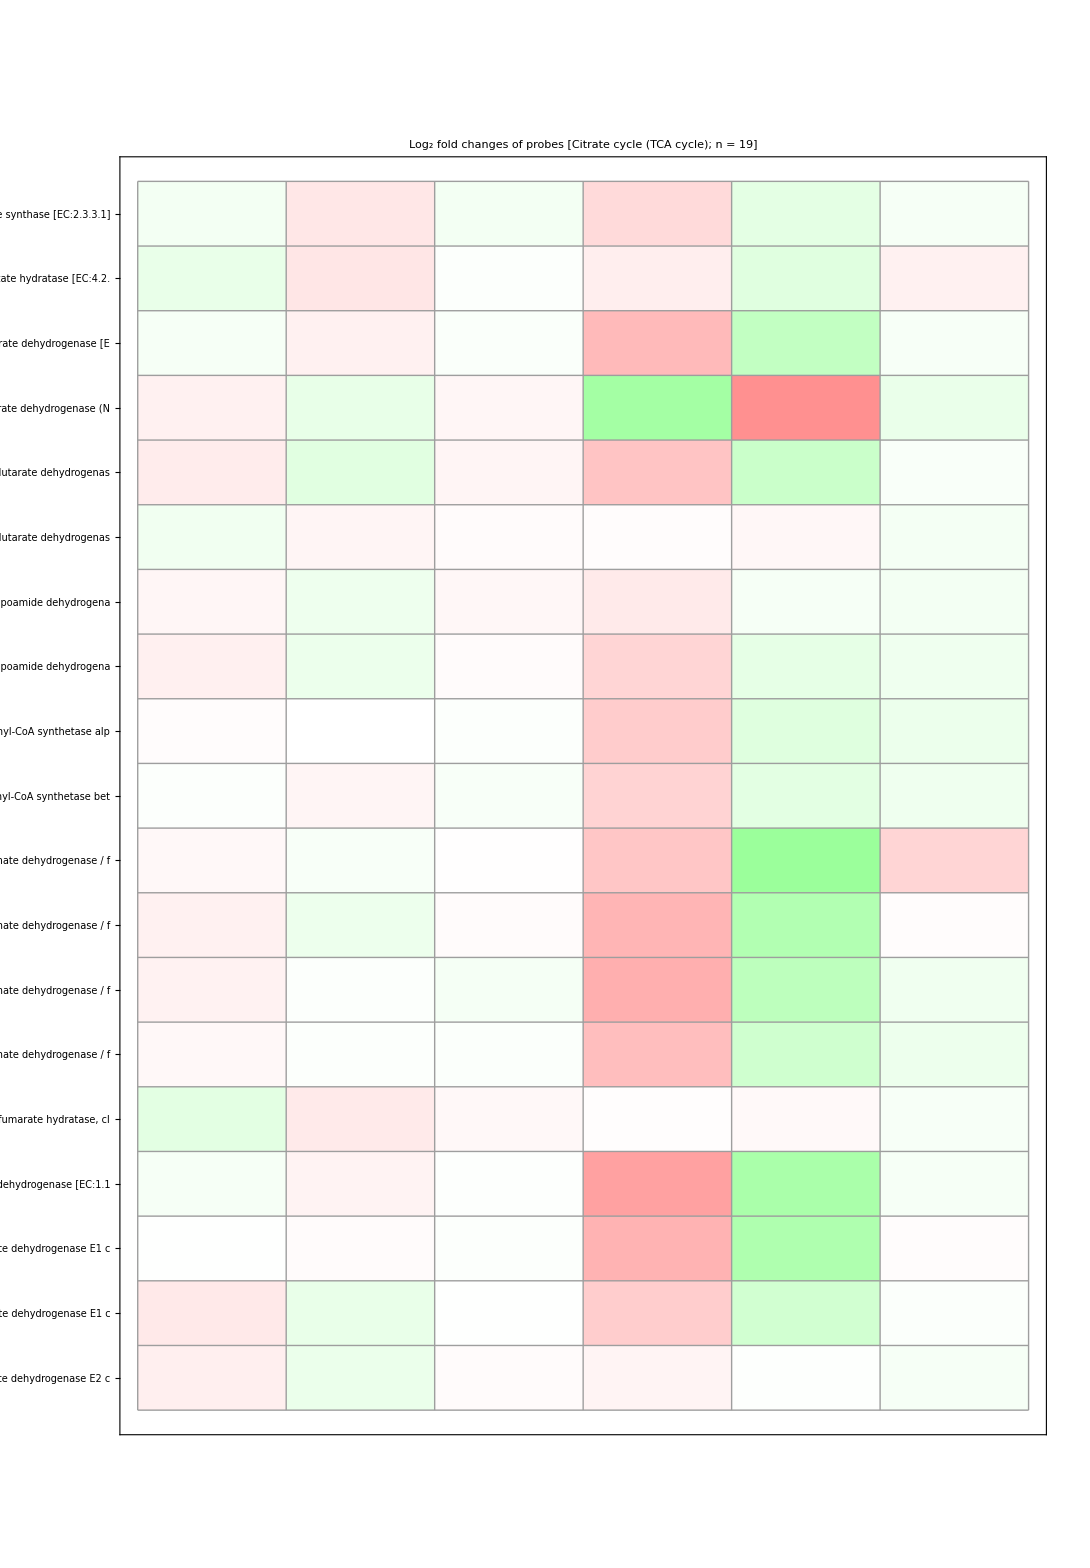

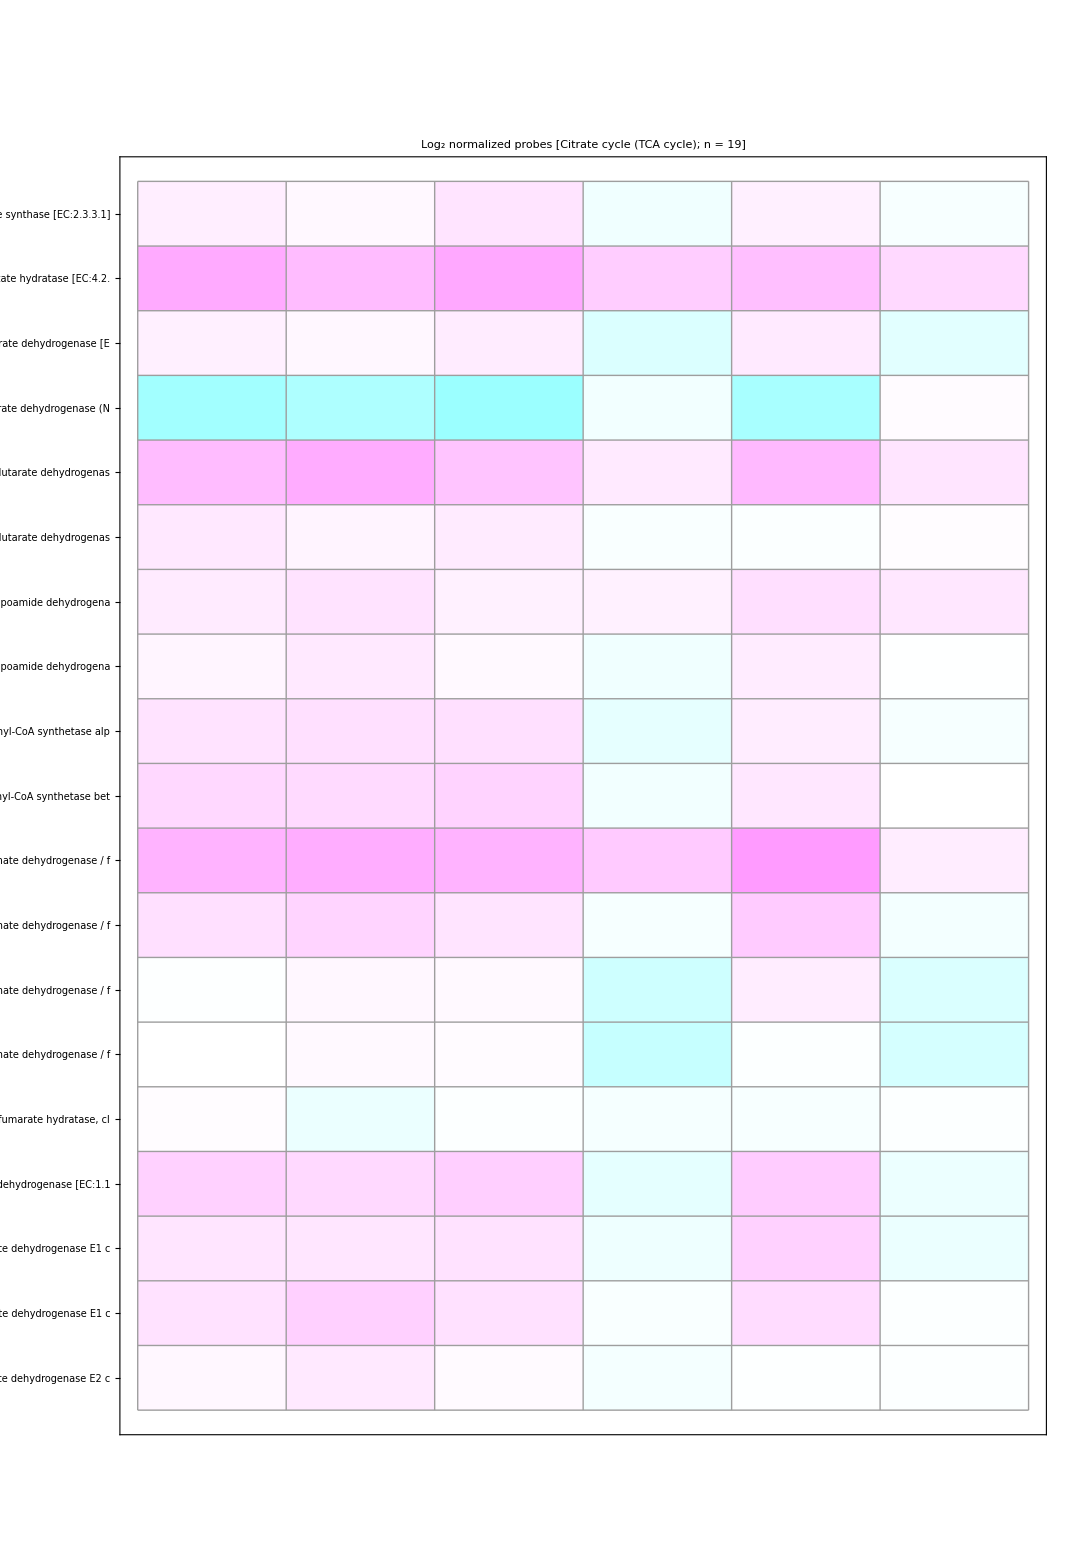

```mathematica
Graphics[{Inset[Show[f[3,1090],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{.1,.6}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[3,1090],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{.1,.6}]]},AspectRatio->Automatic]
```

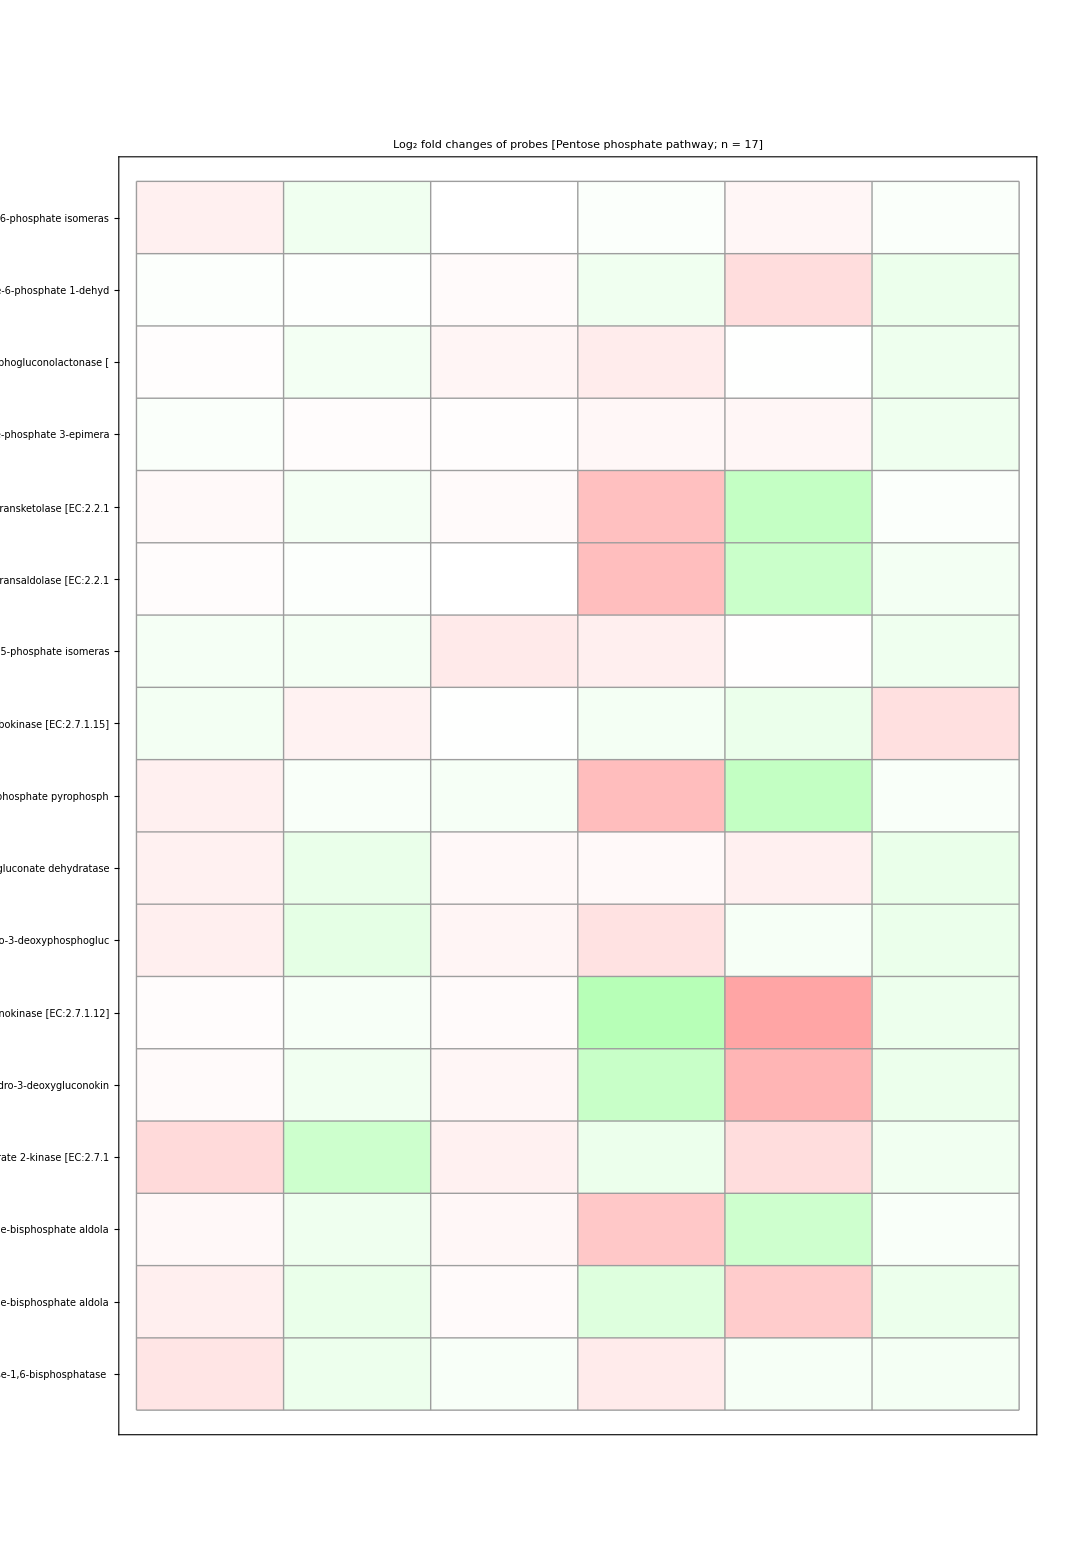

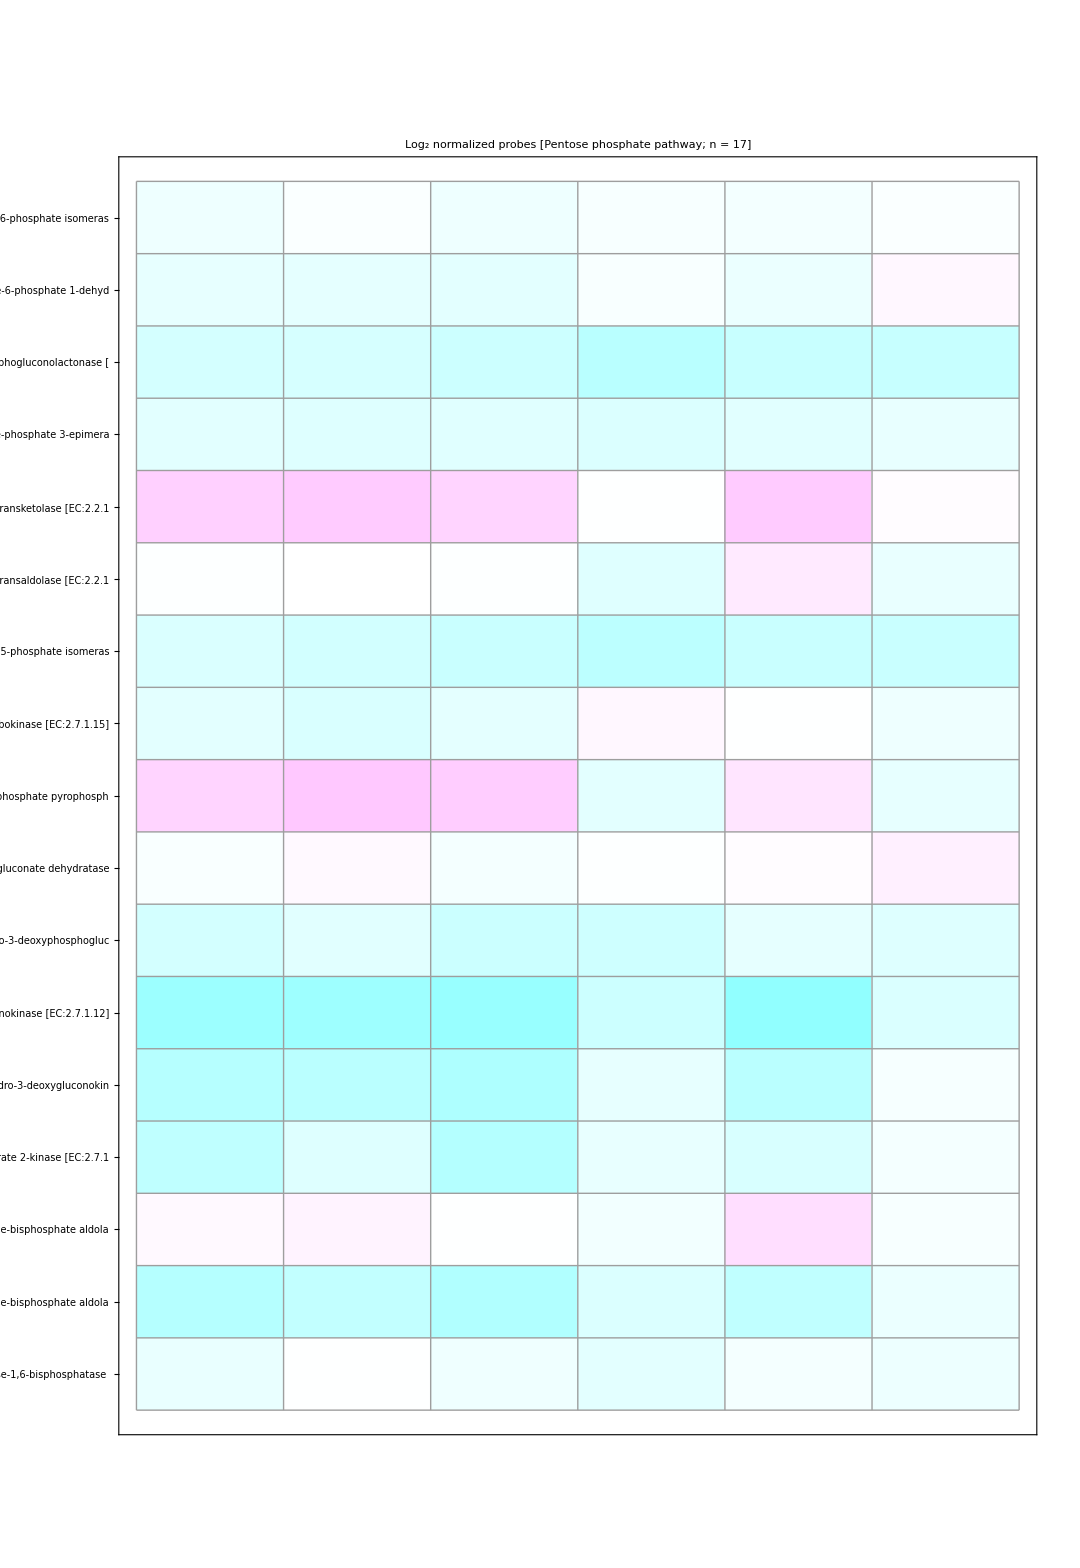

```mathematica
Graphics[{Inset[Show[f[4,1080],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{.1,.5}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[4,1080],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{.1,.5}]]},AspectRatio->Automatic]
```

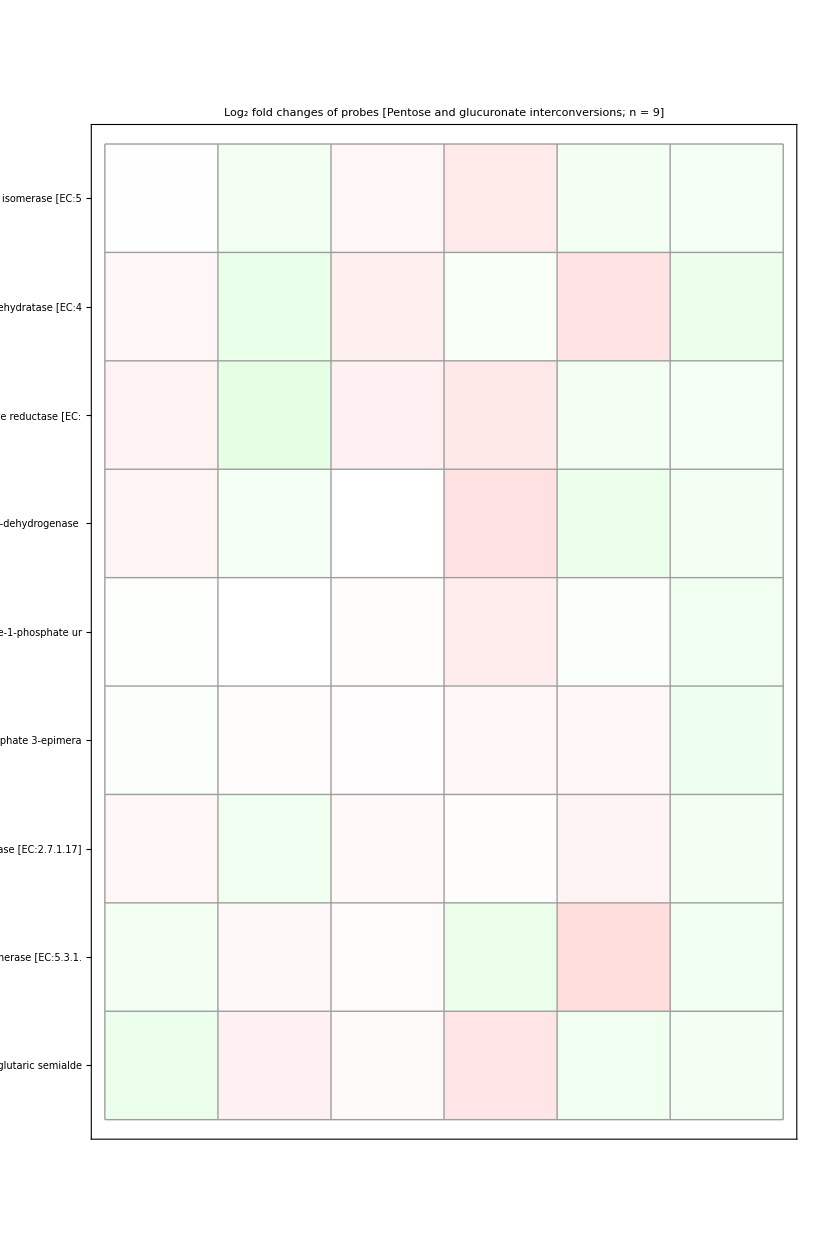

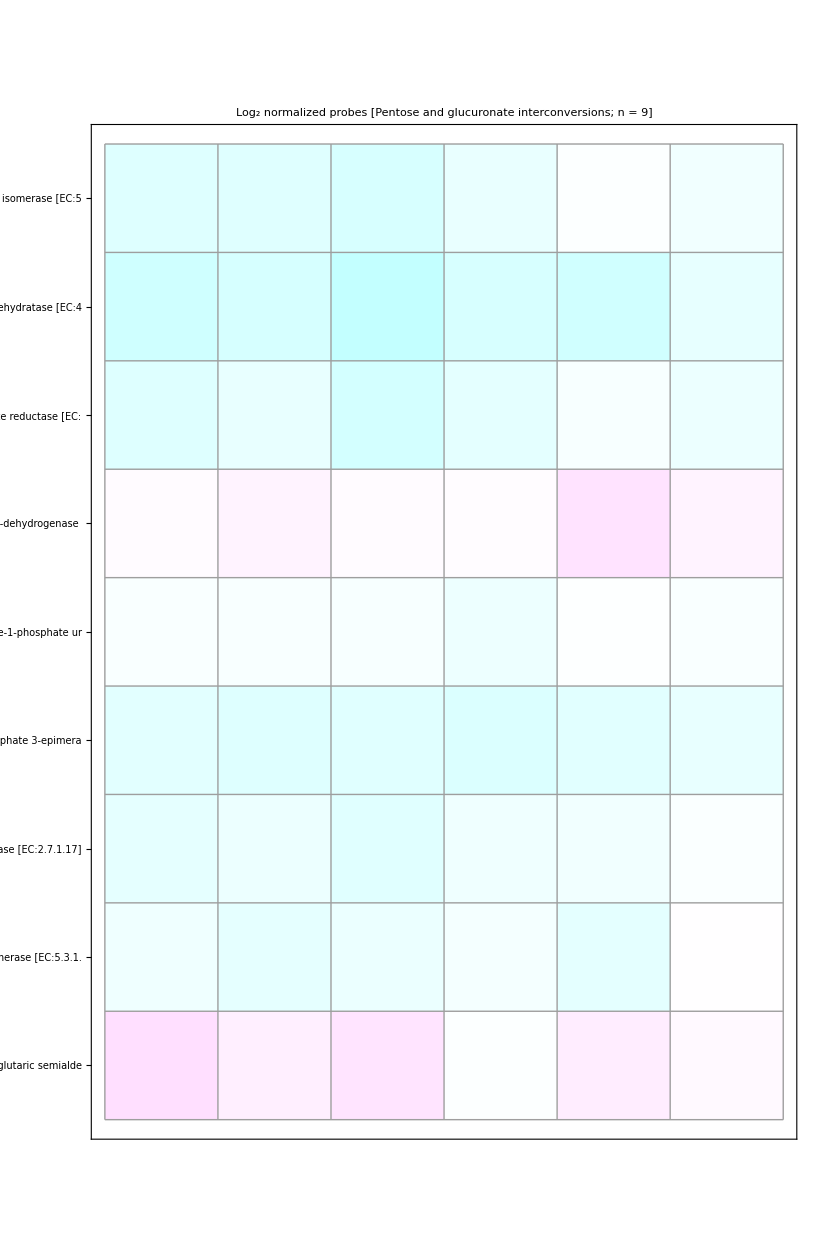

```mathematica
Graphics[{Inset[Show[f[5,830],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{.1,.5}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[5,830],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{.1,.5}]]},AspectRatio->Automatic]
```

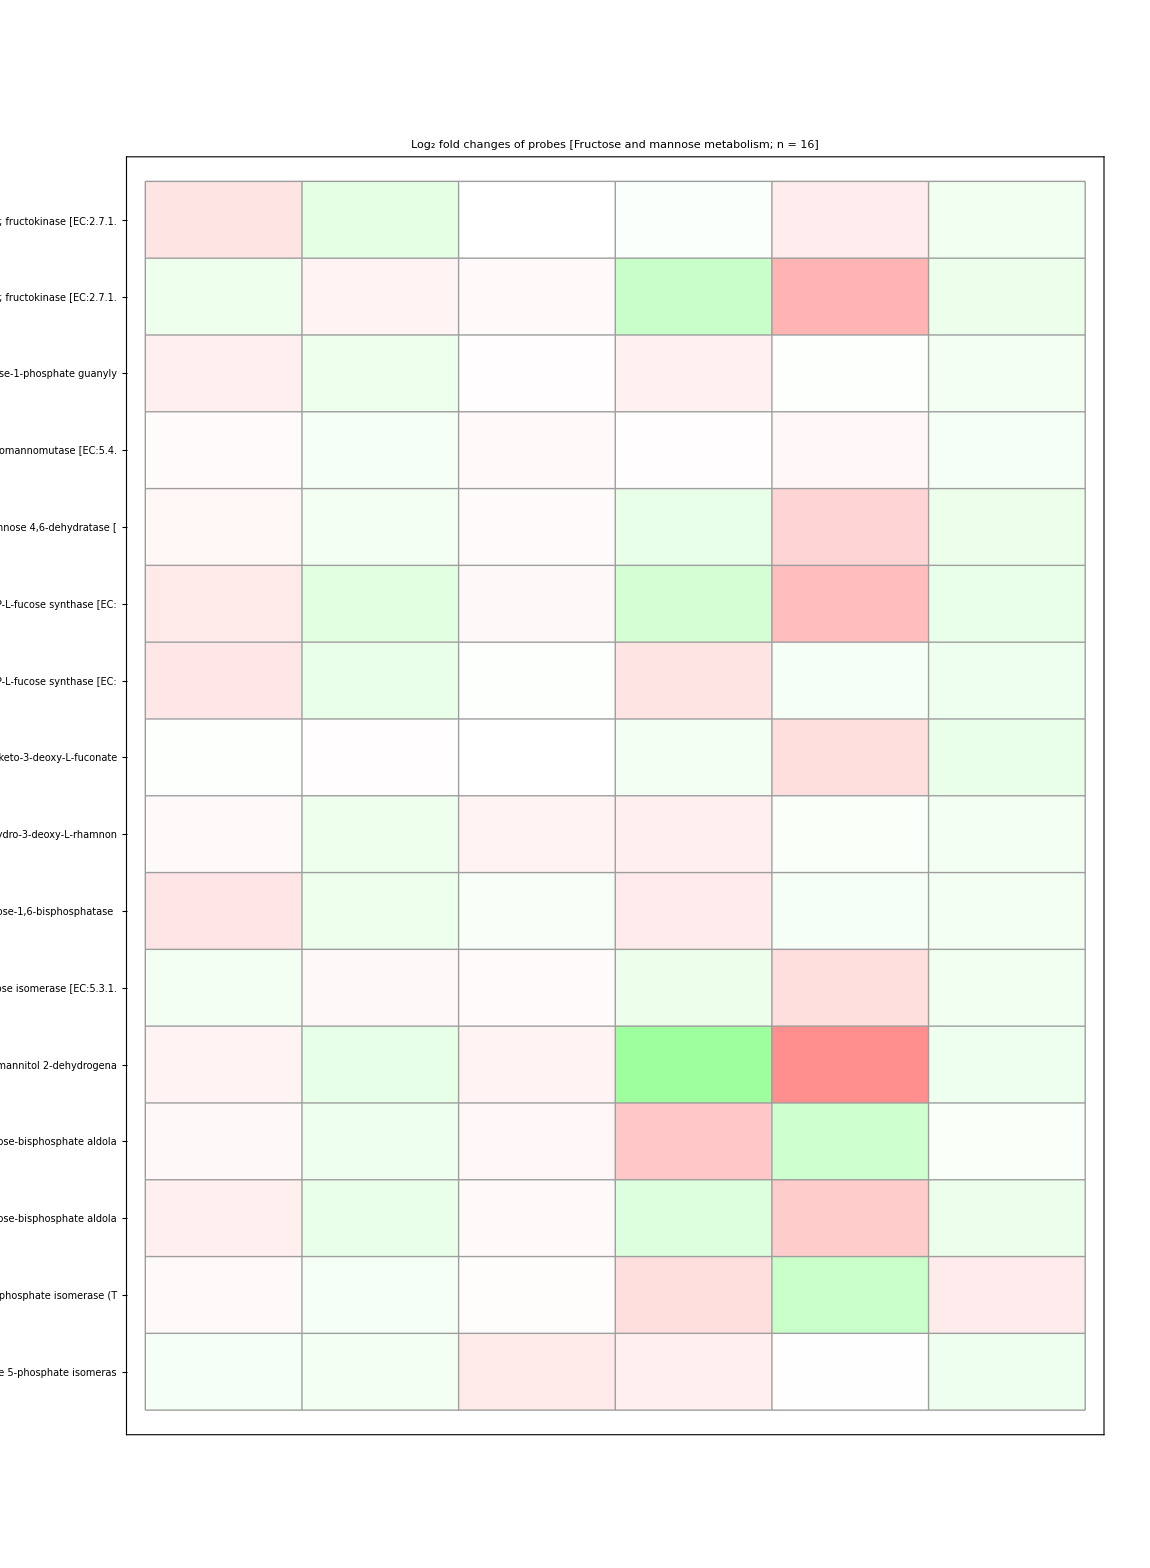

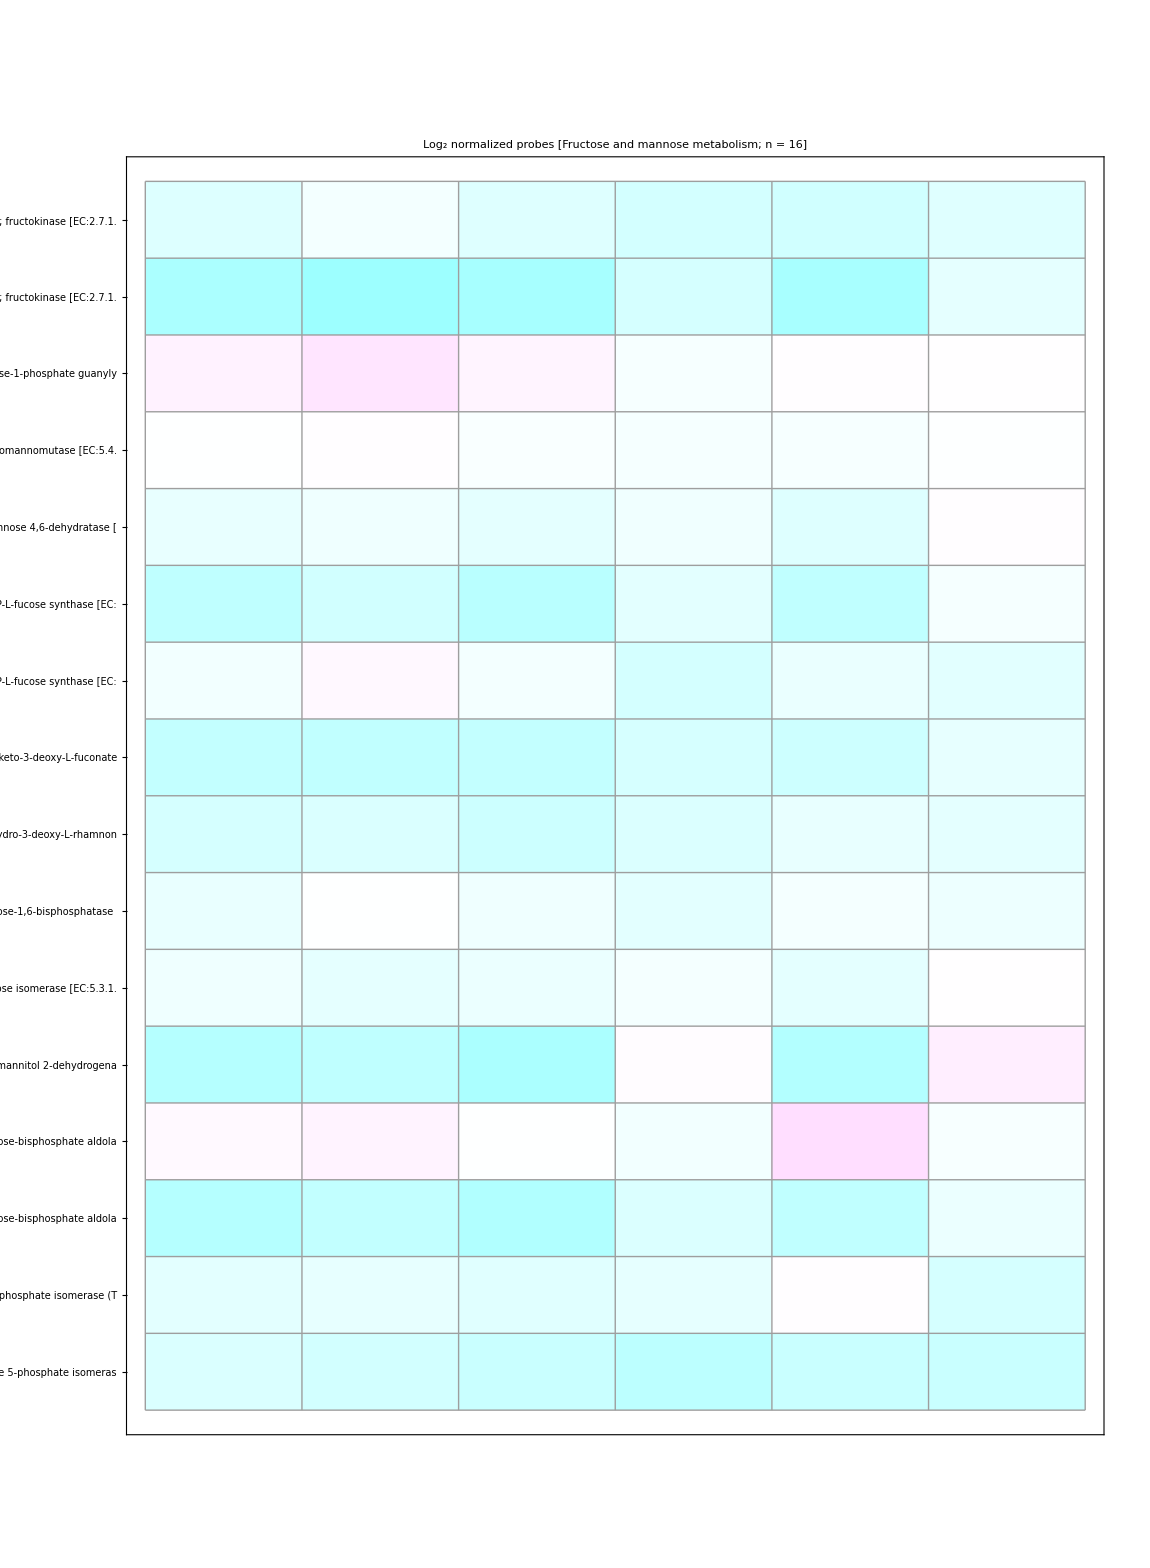

```mathematica
Graphics[{Inset[Show[f[6,1150],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{.1,.55}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[6,1150],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{.1,.55}]]},AspectRatio->Automatic]
```

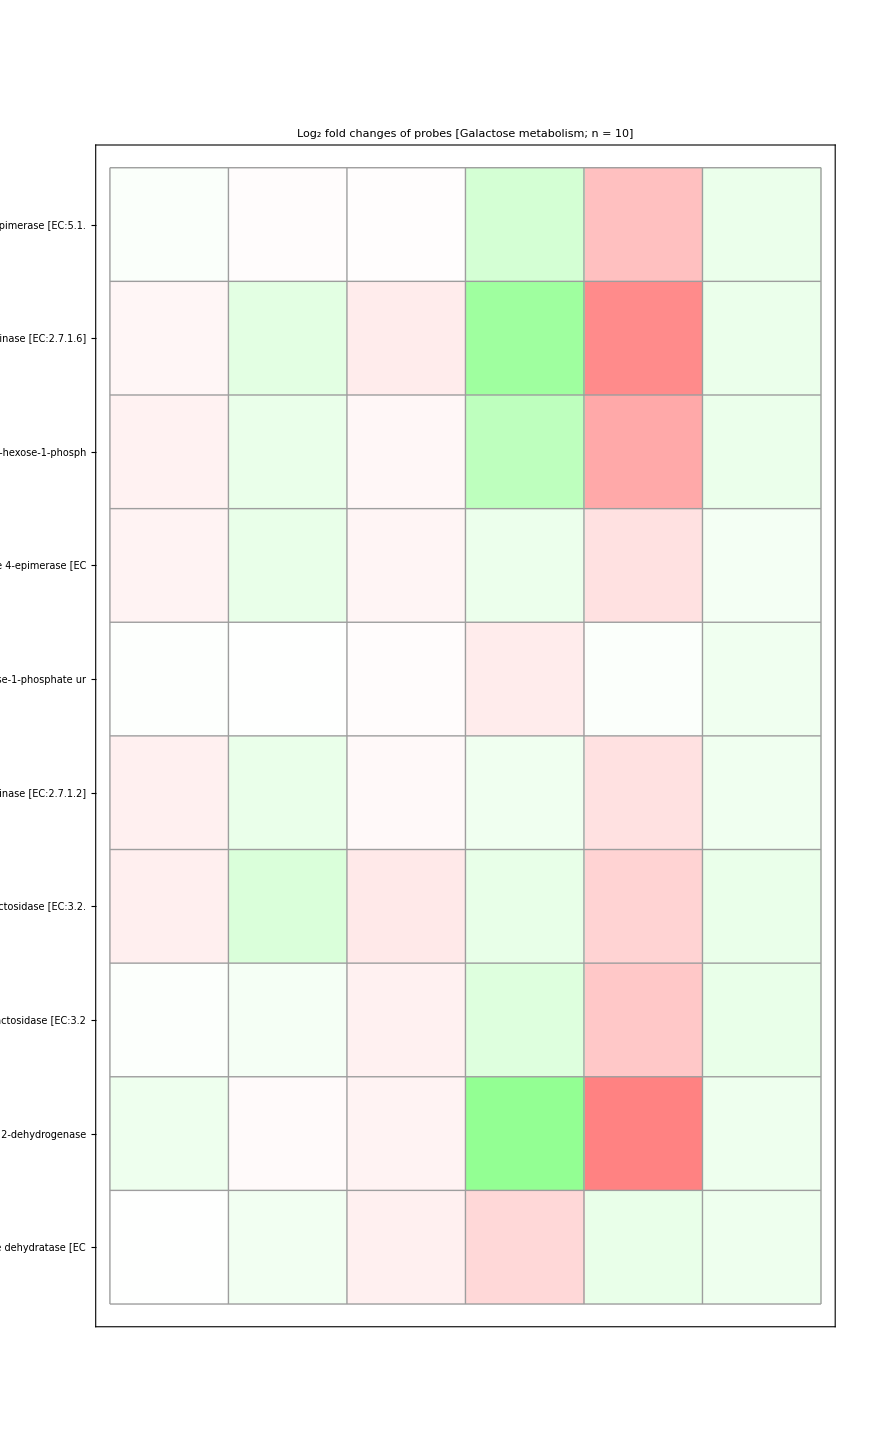

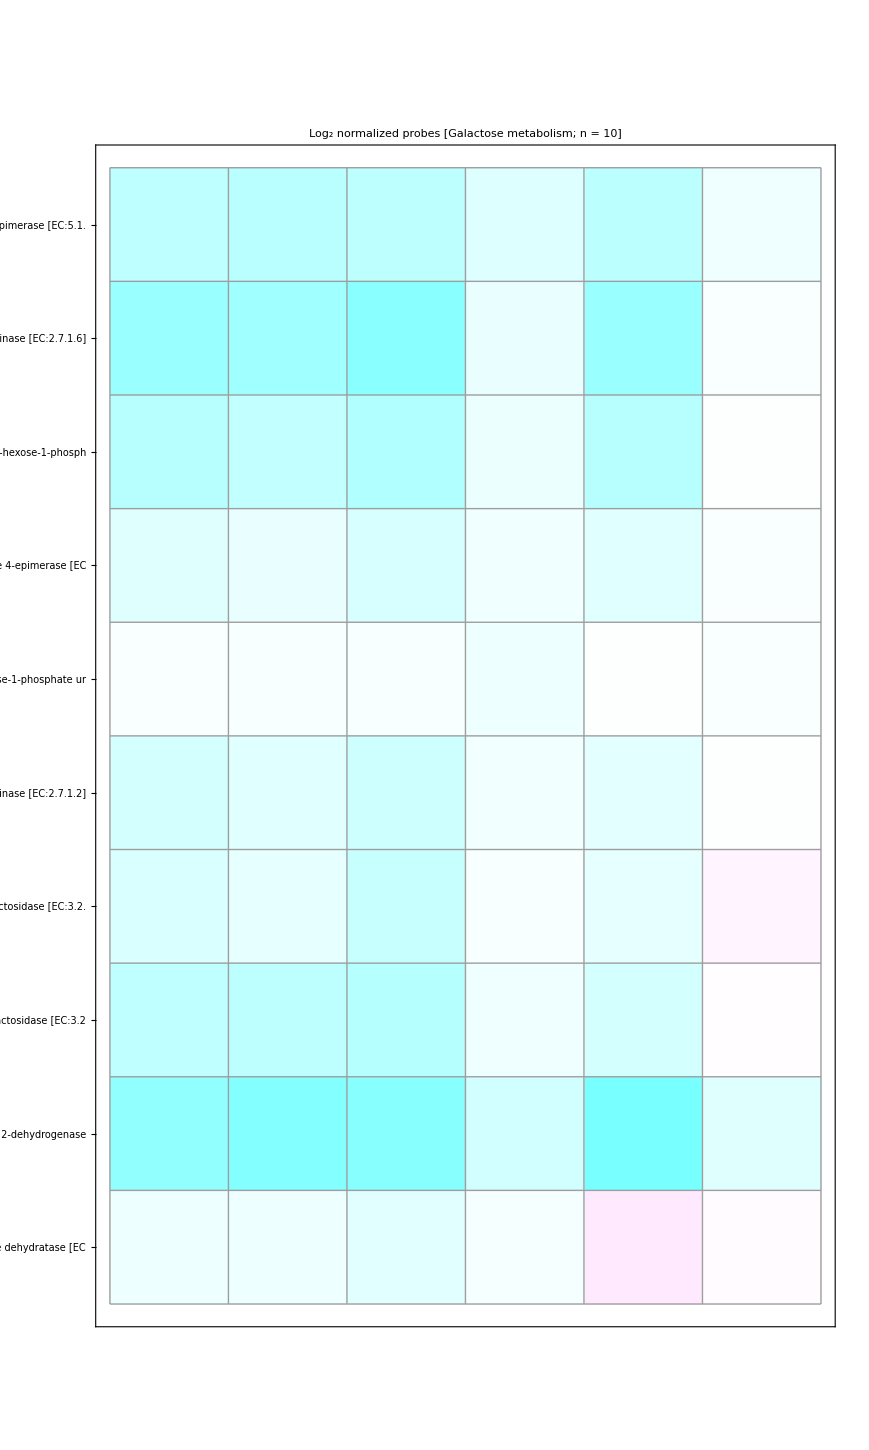

```mathematica
Graphics[{Inset[Show[f[7,870],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{.1,.6}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[7,870],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{.1,.6}]]},AspectRatio->Automatic]
```

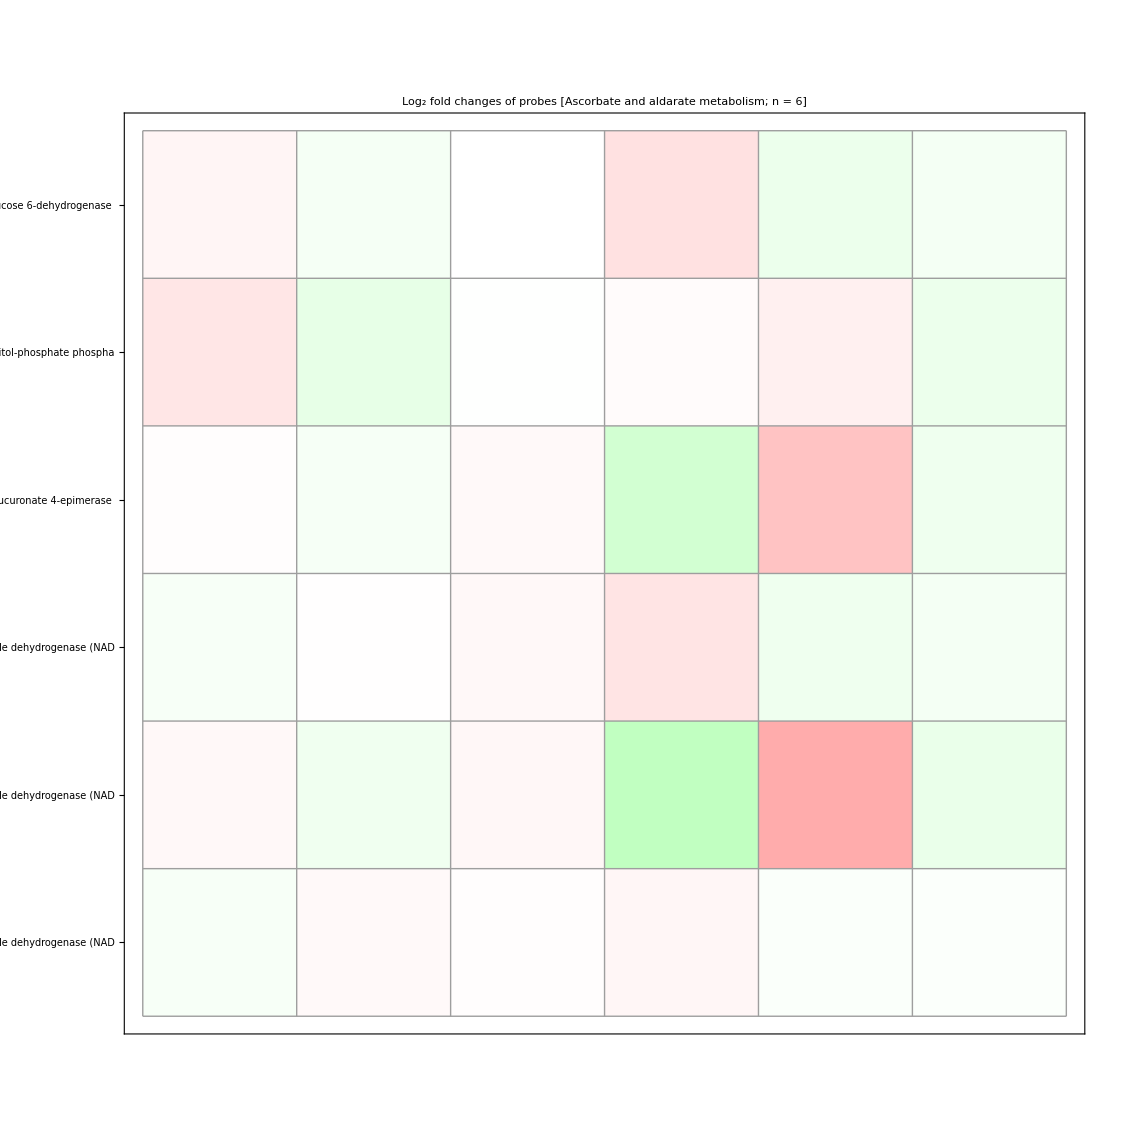

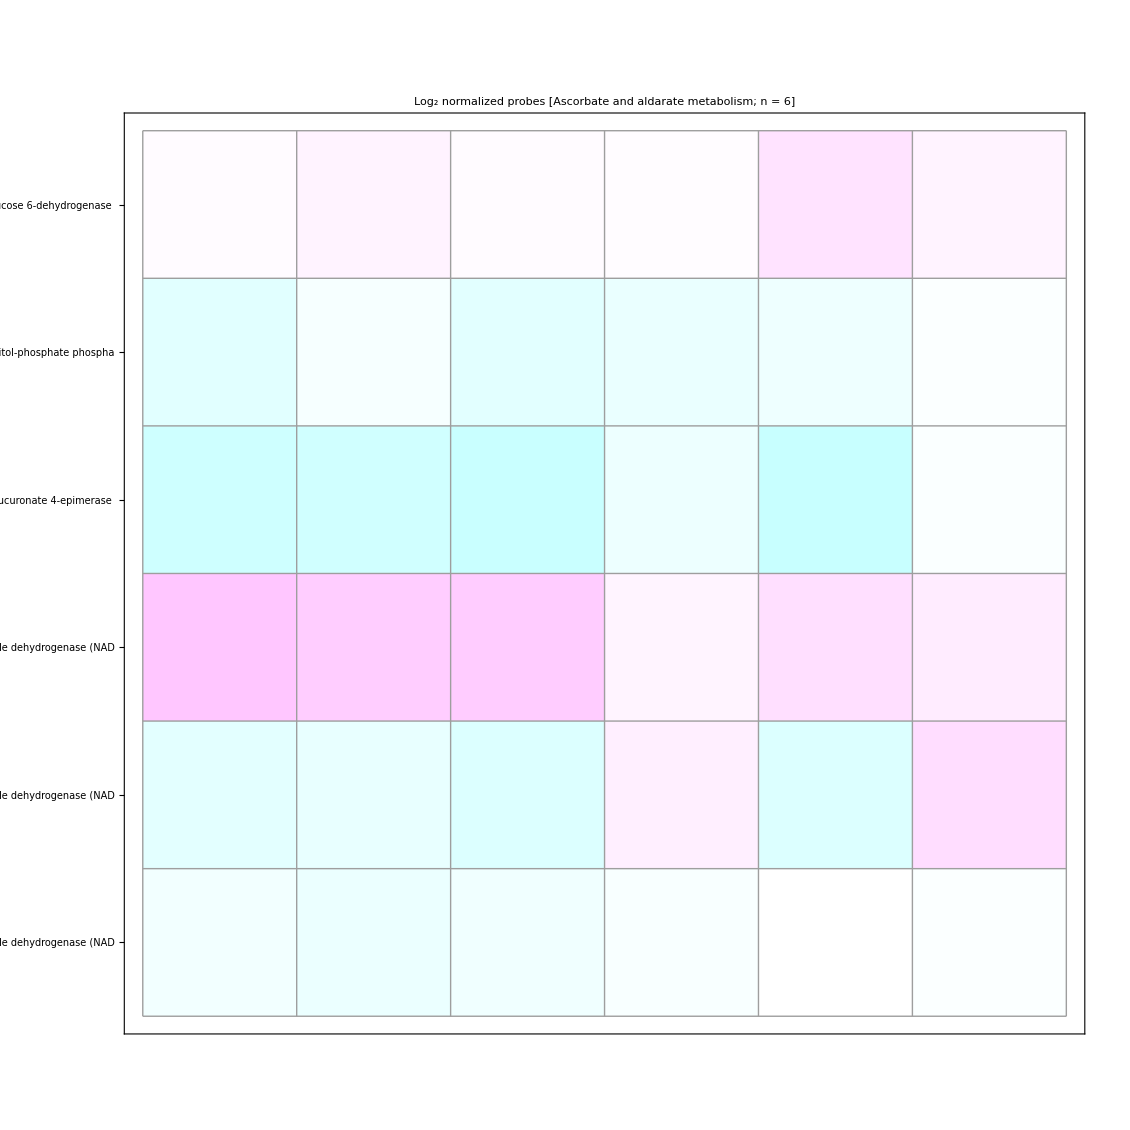

```mathematica
Graphics[{Inset[Show[f[8,1130],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{0.2,.45}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[8,1130],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{0.2,.45}]]},AspectRatio->Automatic]
```

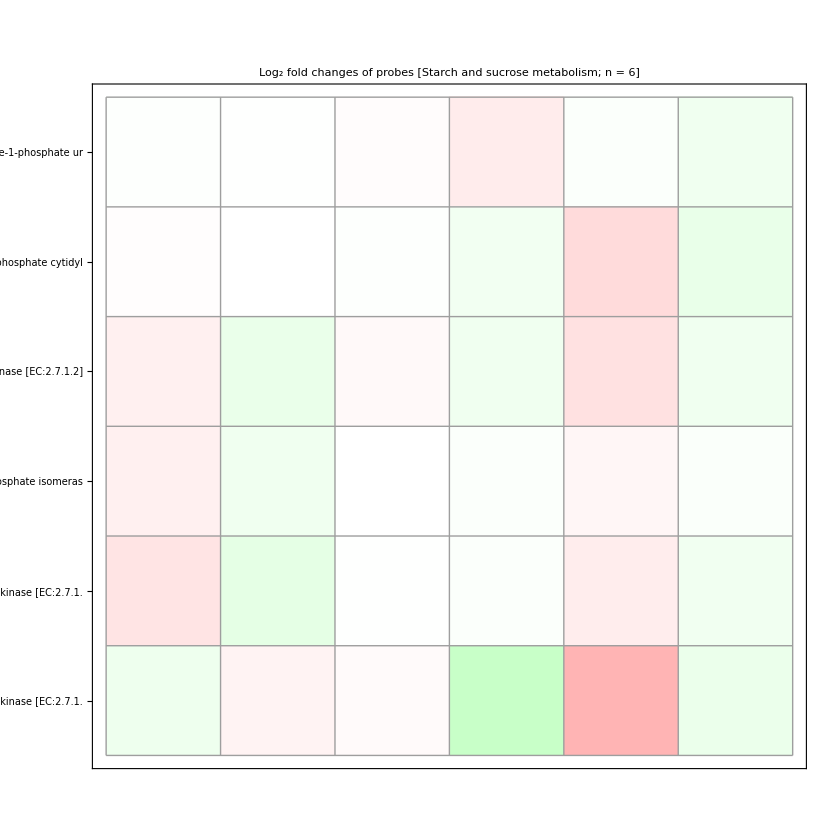

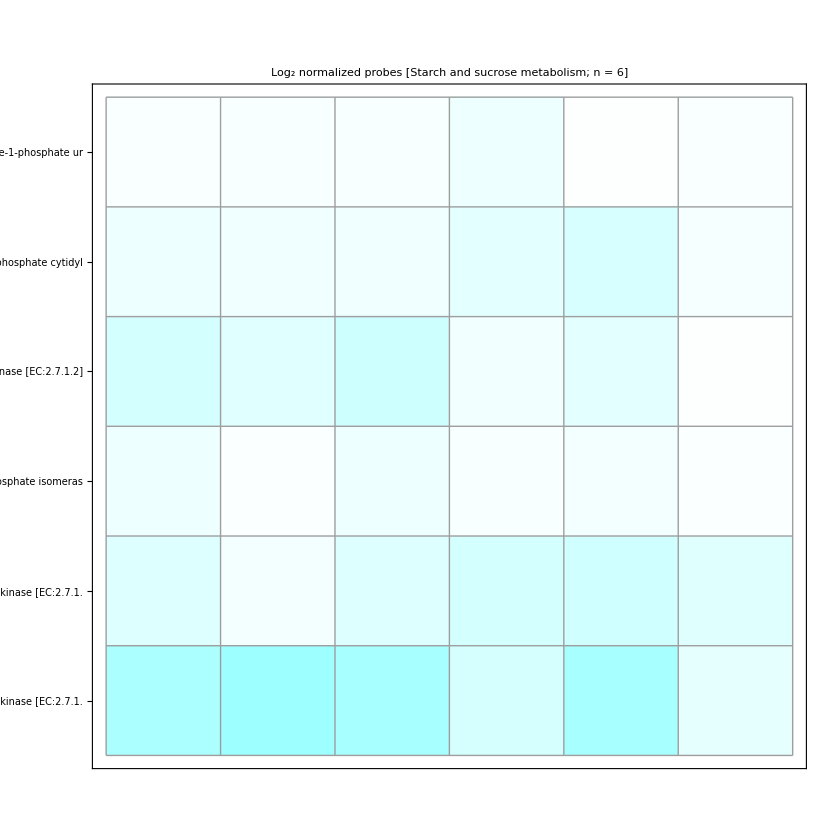

```mathematica
Graphics[{Inset[Show[f[9,840],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{0,.6}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[9,840],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{0,.6}]]},AspectRatio->Automatic]
```

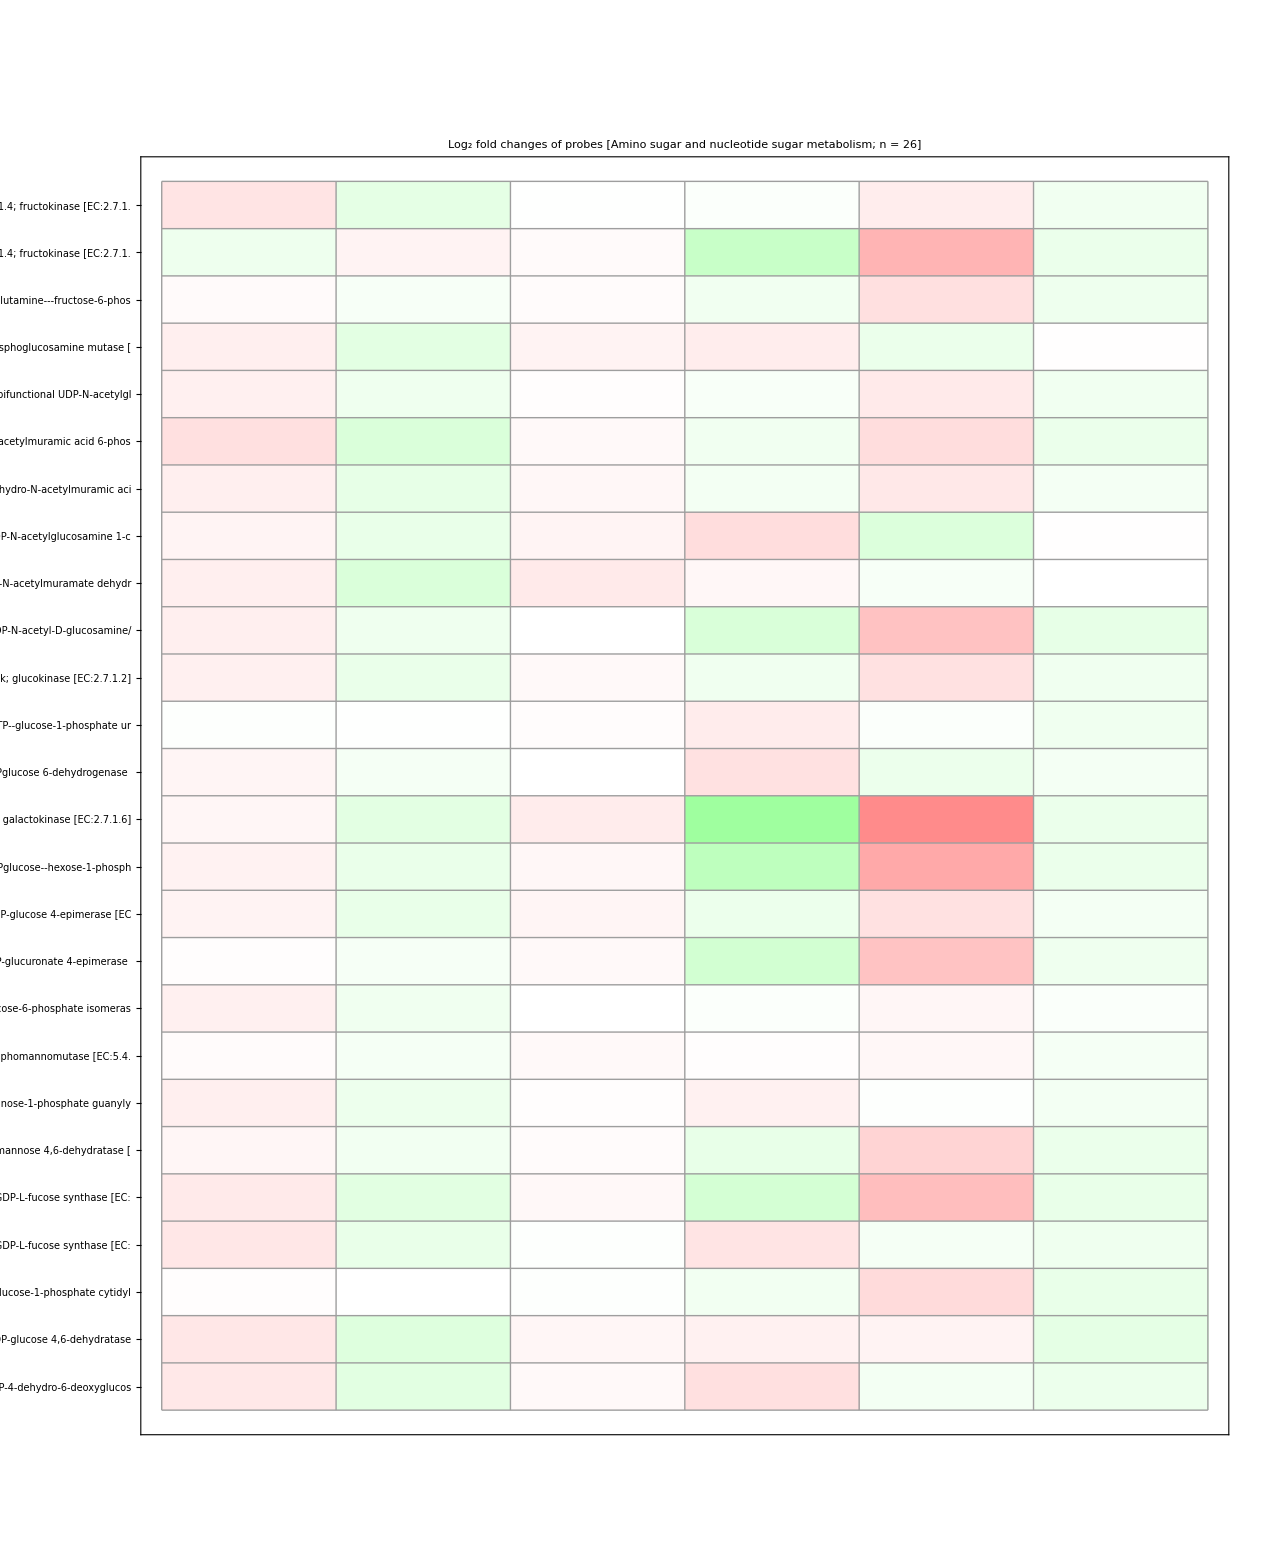

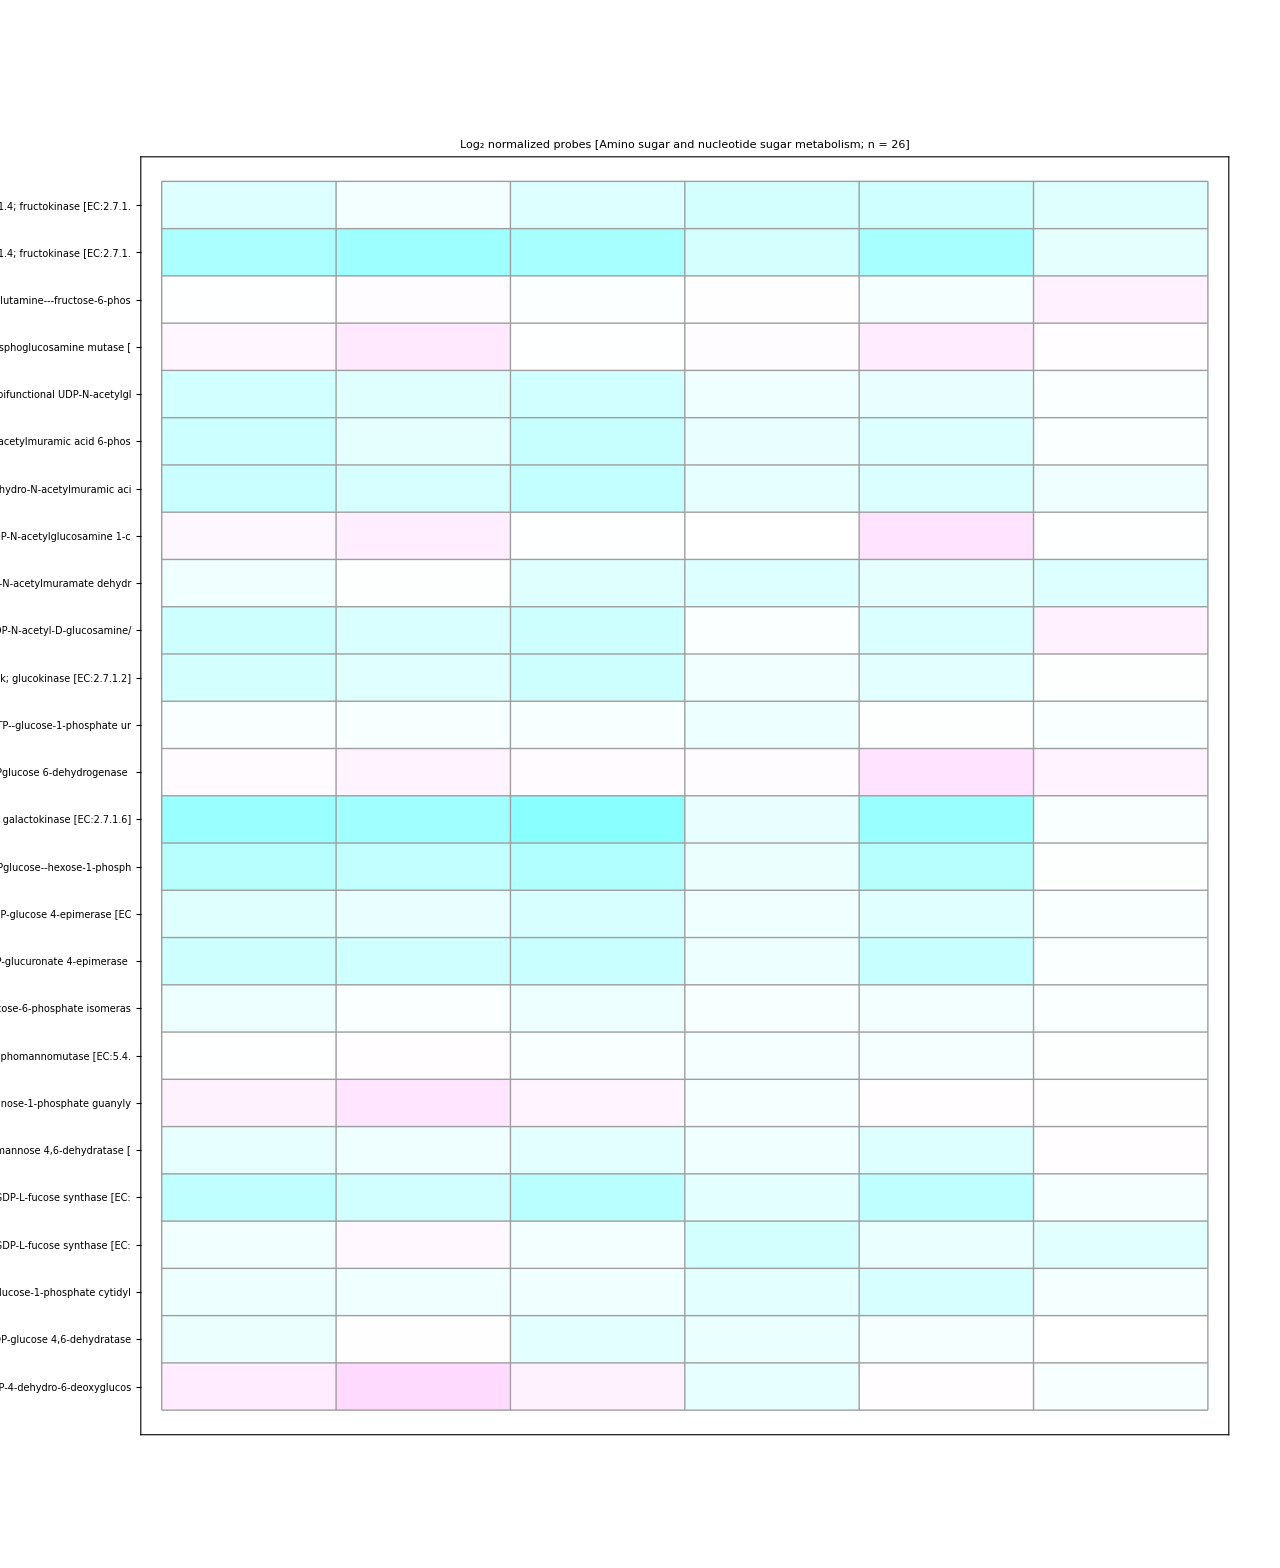

```mathematica
Graphics[{Inset[Show[f[10,1280],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{0,.5}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[10,1280],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{0,.5}]]},AspectRatio->Automatic]
```

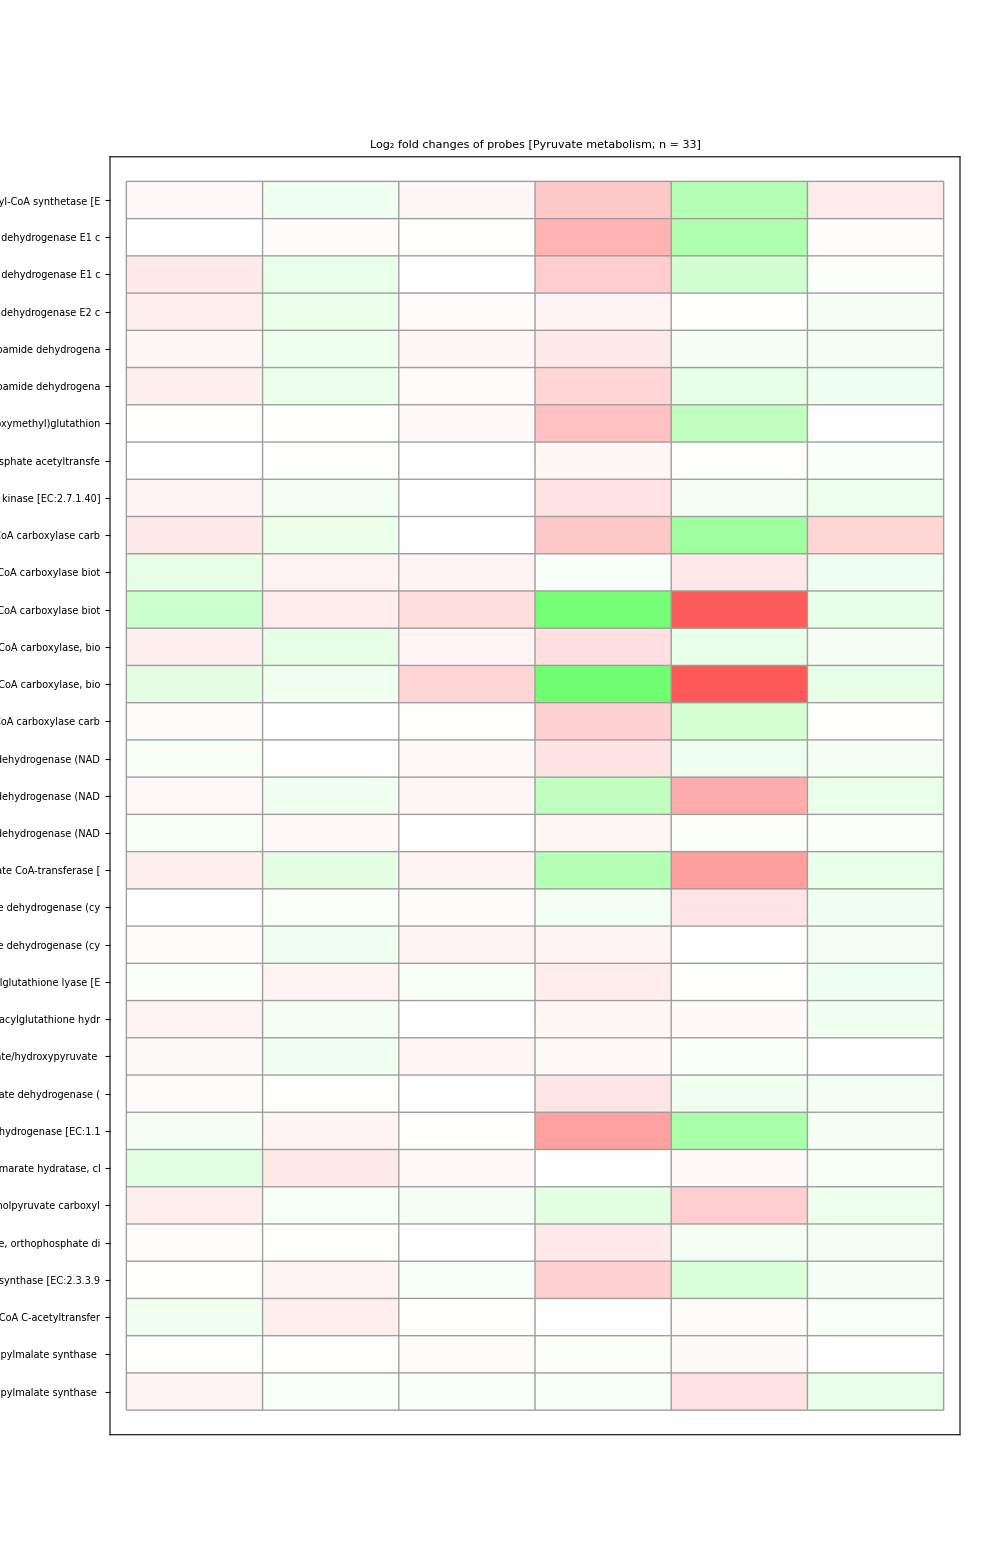

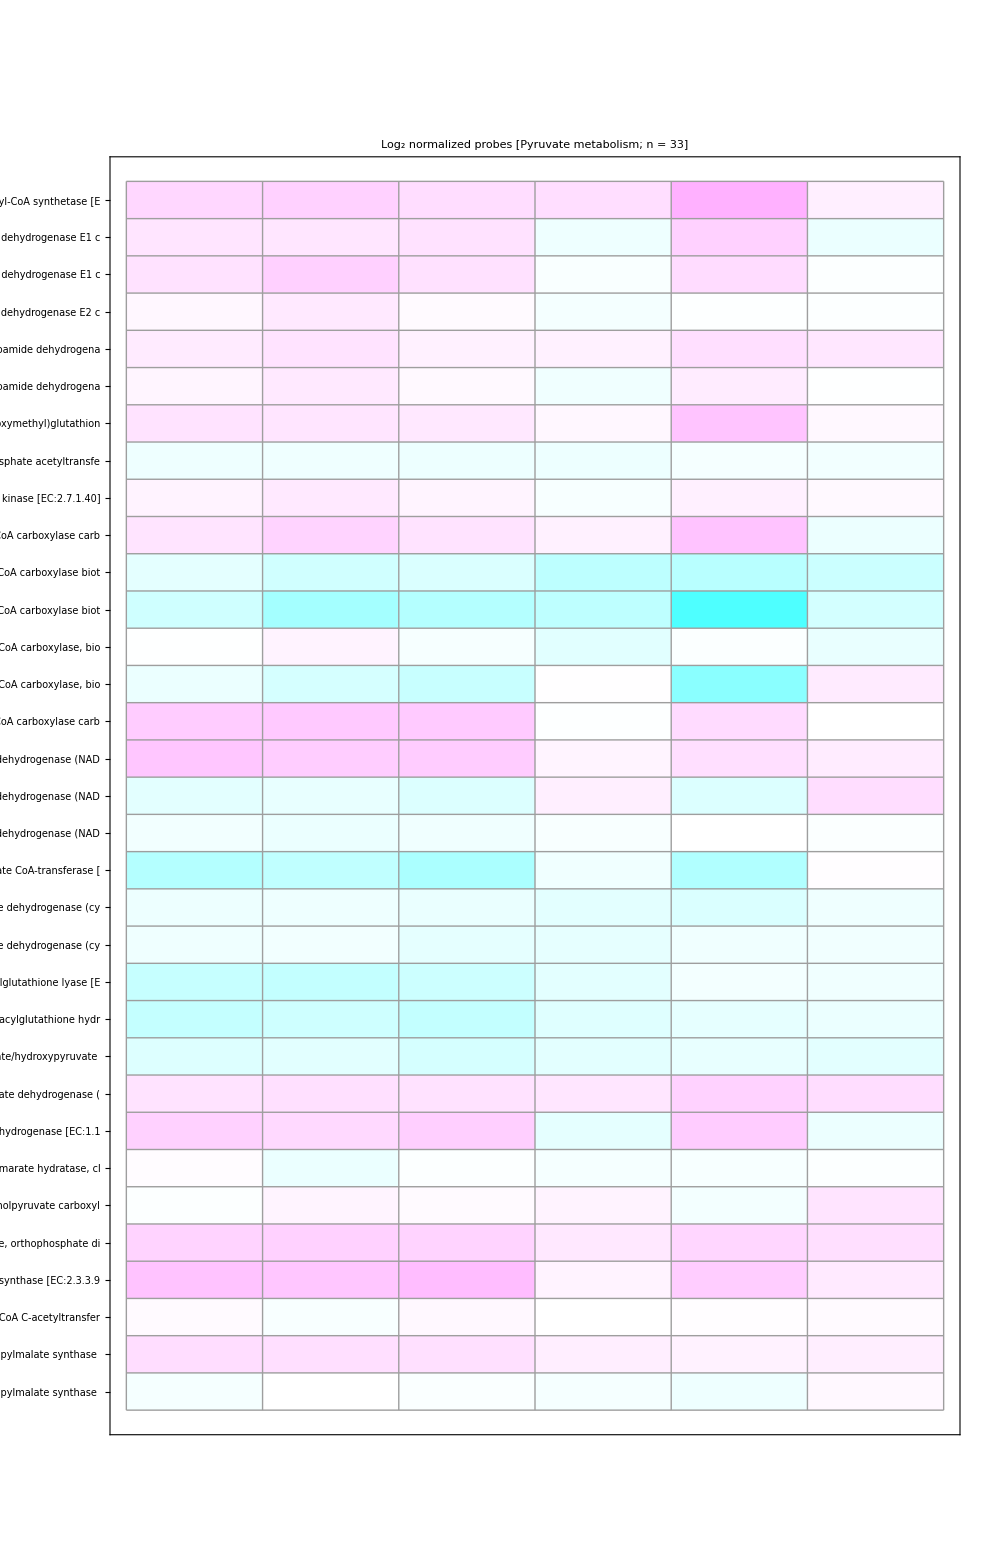

```mathematica
Graphics[{Inset[Show[f[11,1000],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{0,.5}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[11,1000],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{0,.5}]]},AspectRatio->Automatic]
```

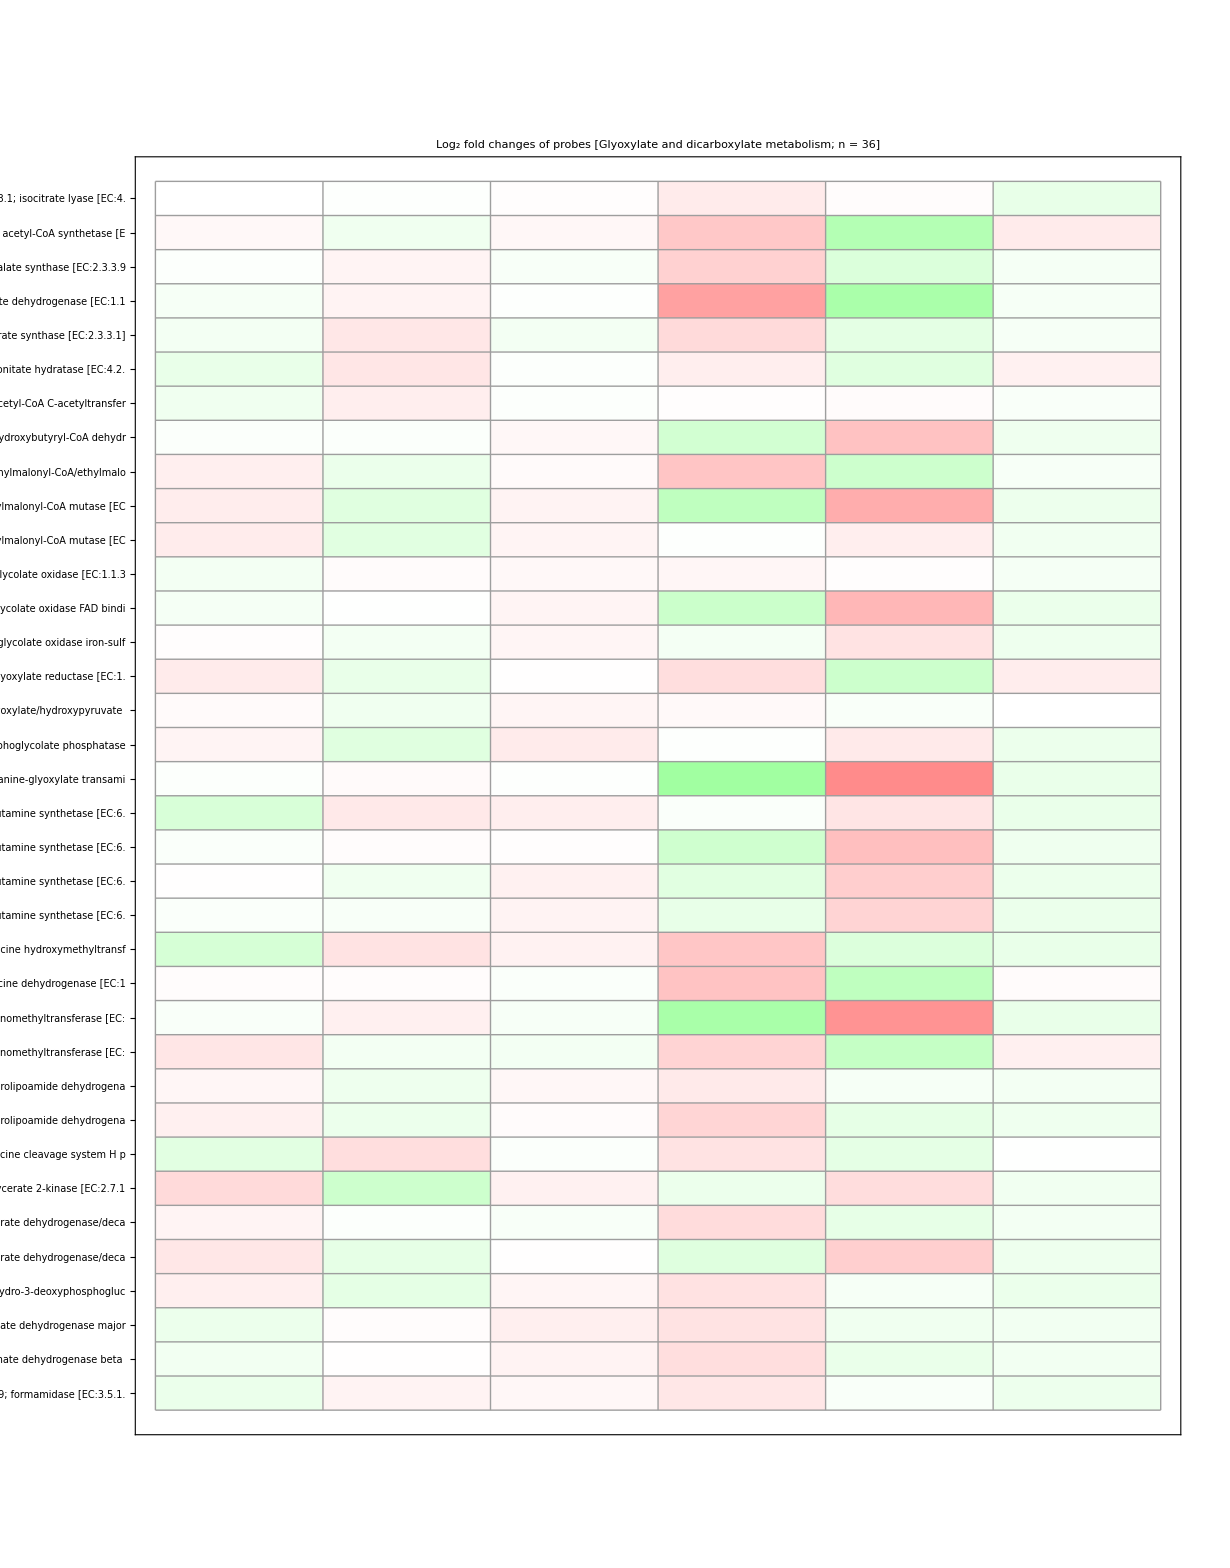

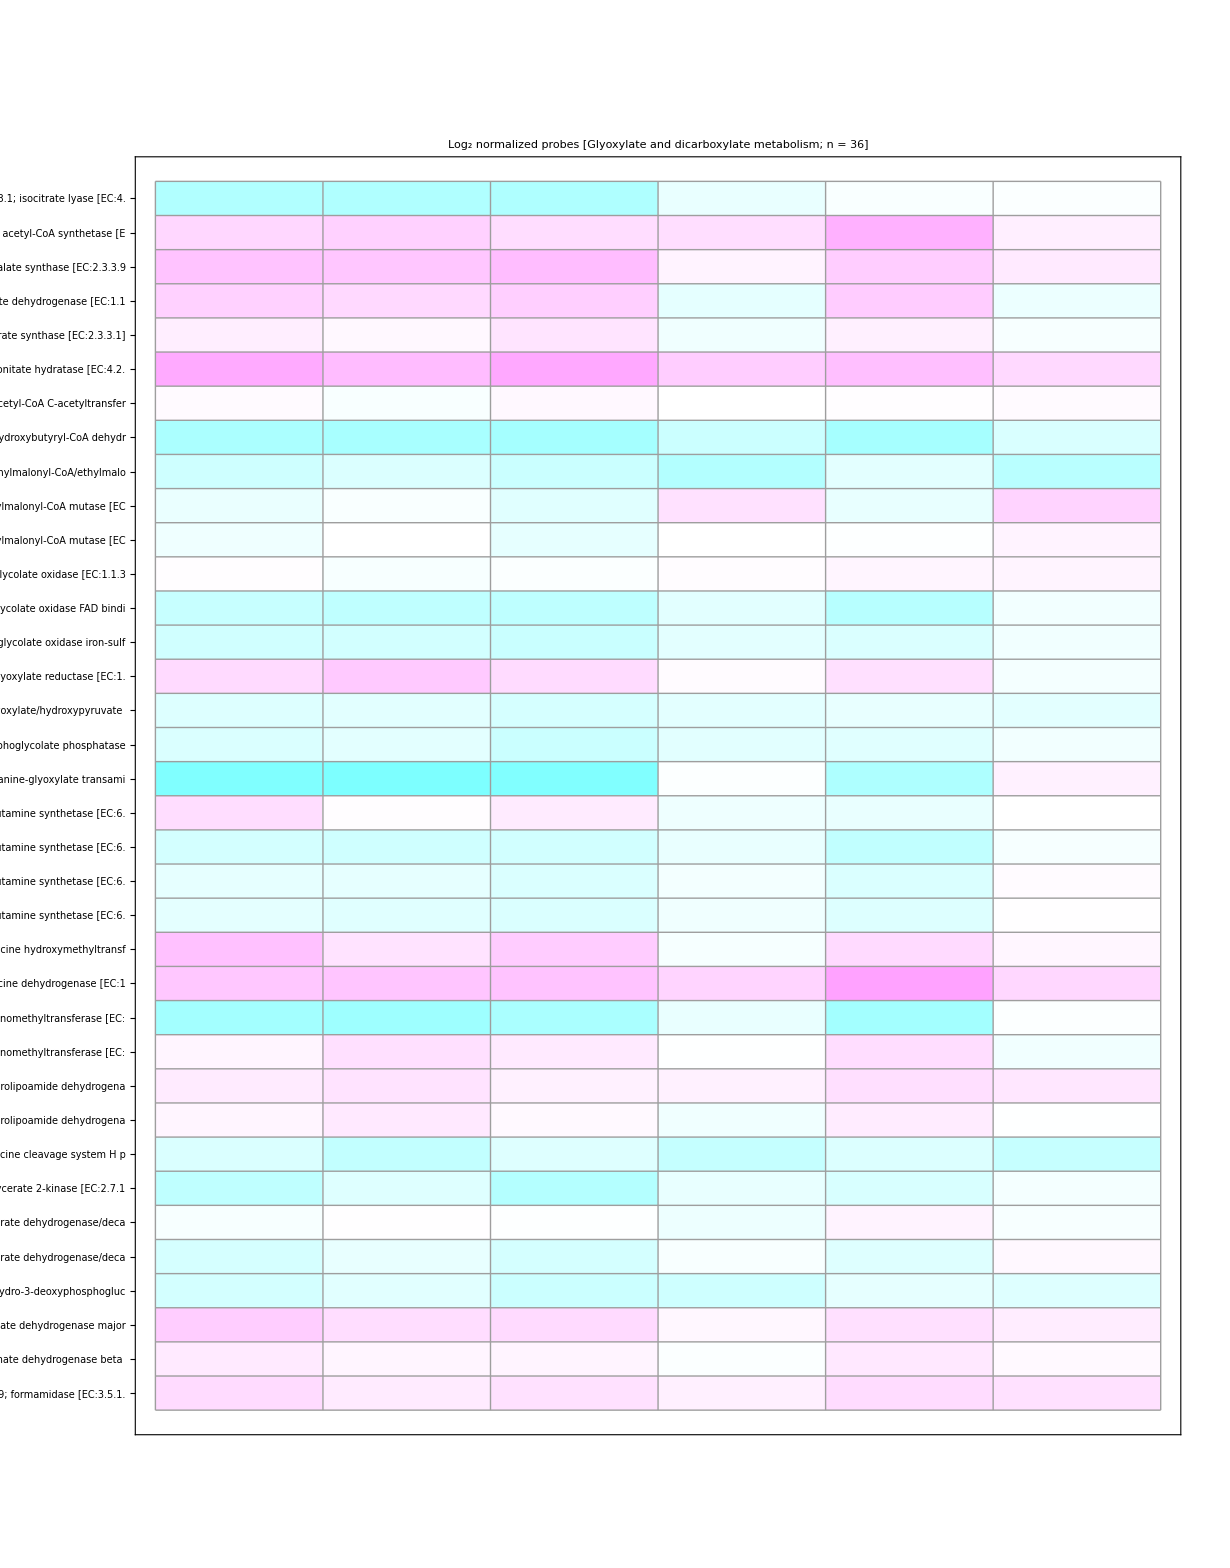

```mathematica
Graphics[{Inset[Show[f[12,1230],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{0,.55}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[12,1230],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{0,.55}]]},AspectRatio->Automatic]
```

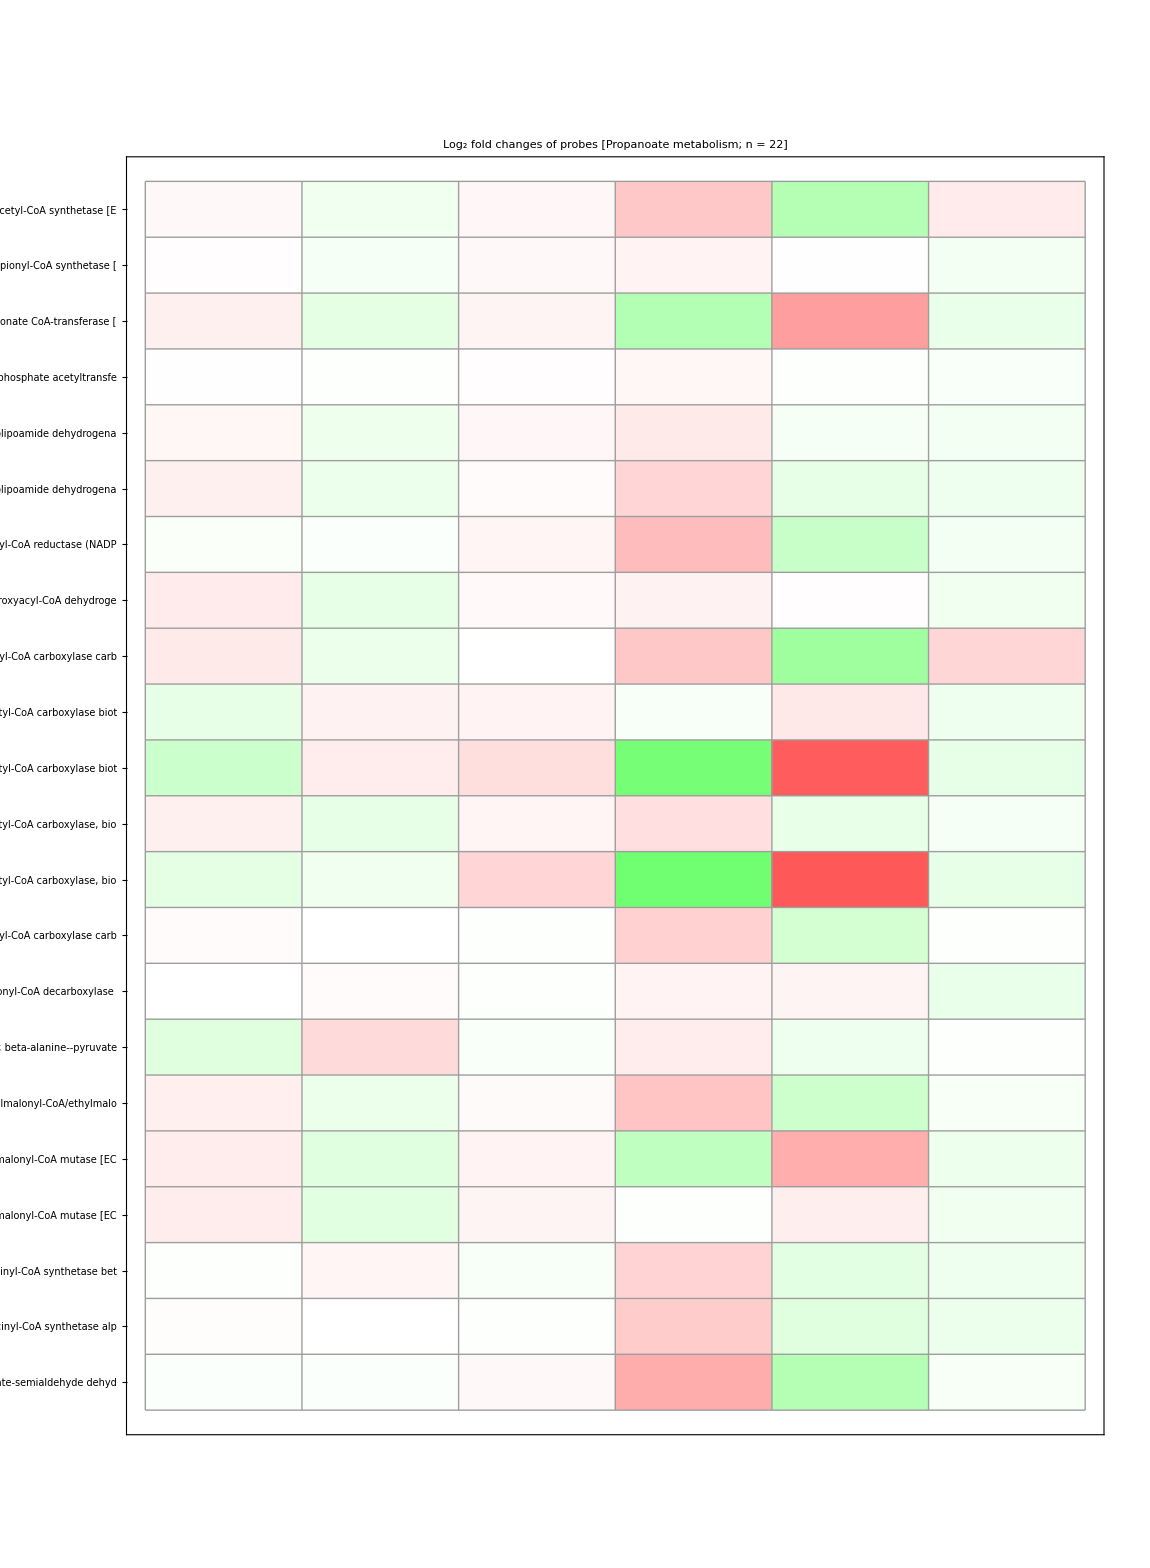

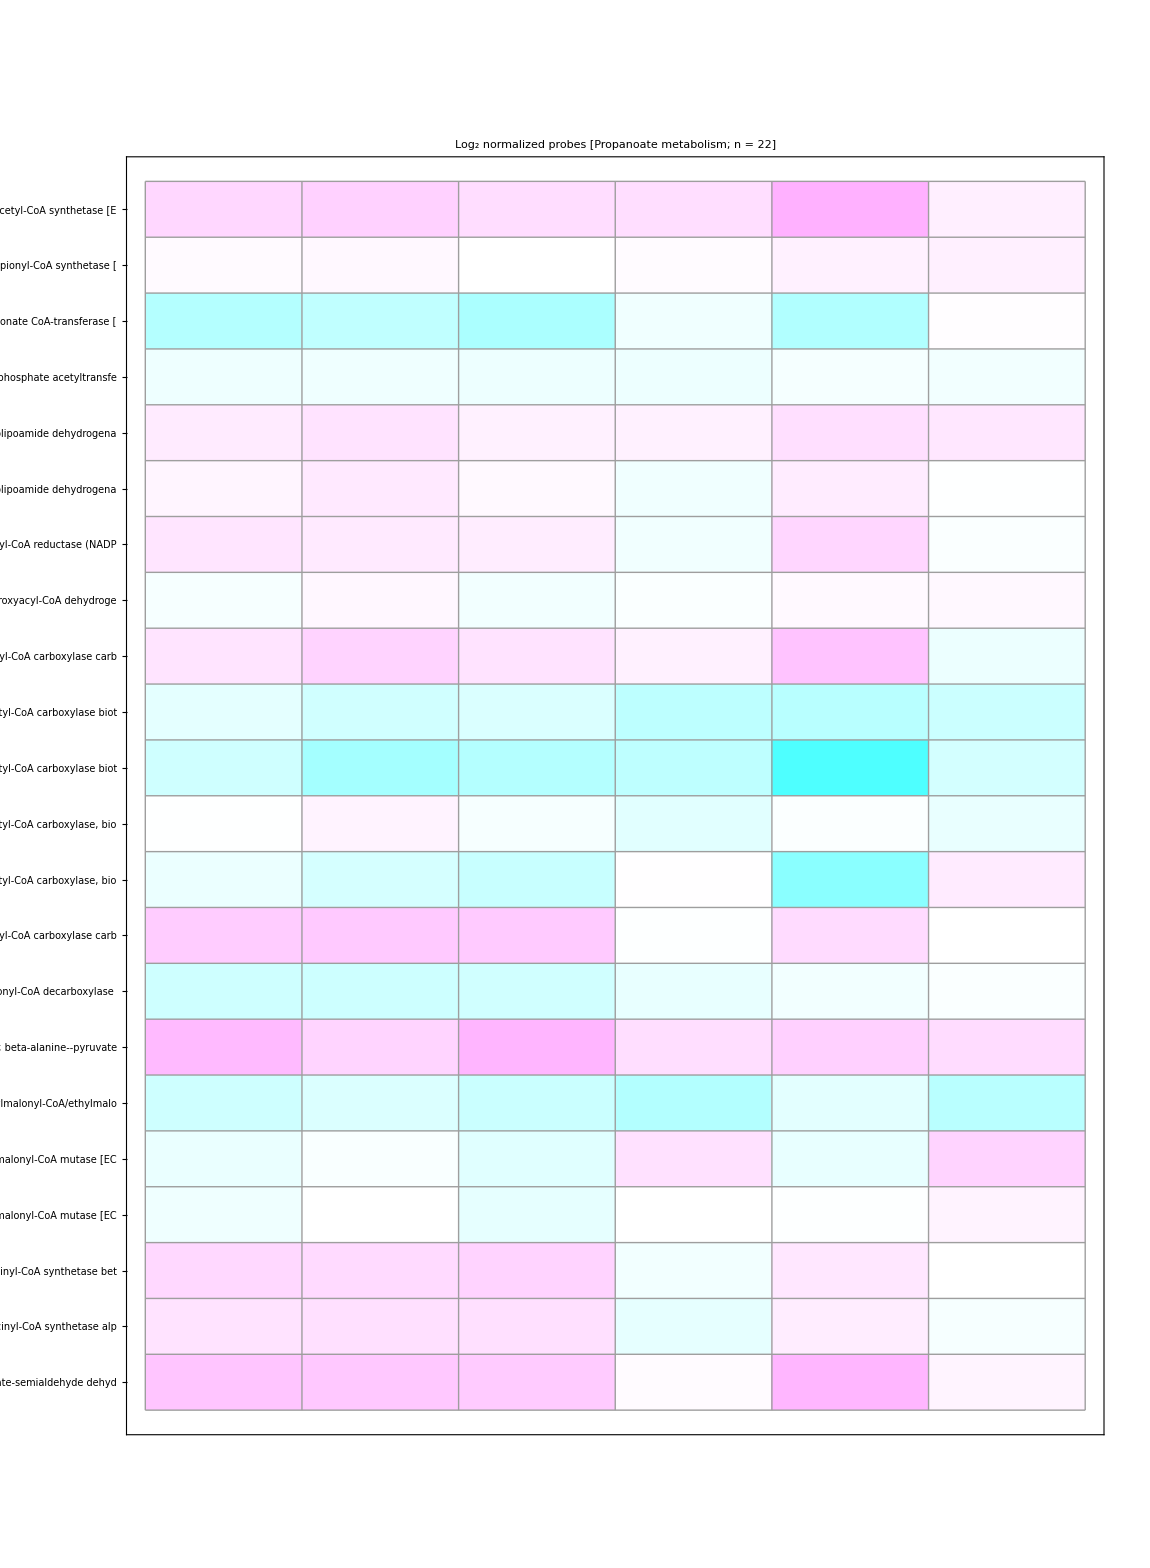

```mathematica
Graphics[{Inset[Show[f[13,1150],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{0,.8}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[13,1150],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{0,.8}]]},AspectRatio->Automatic]
```

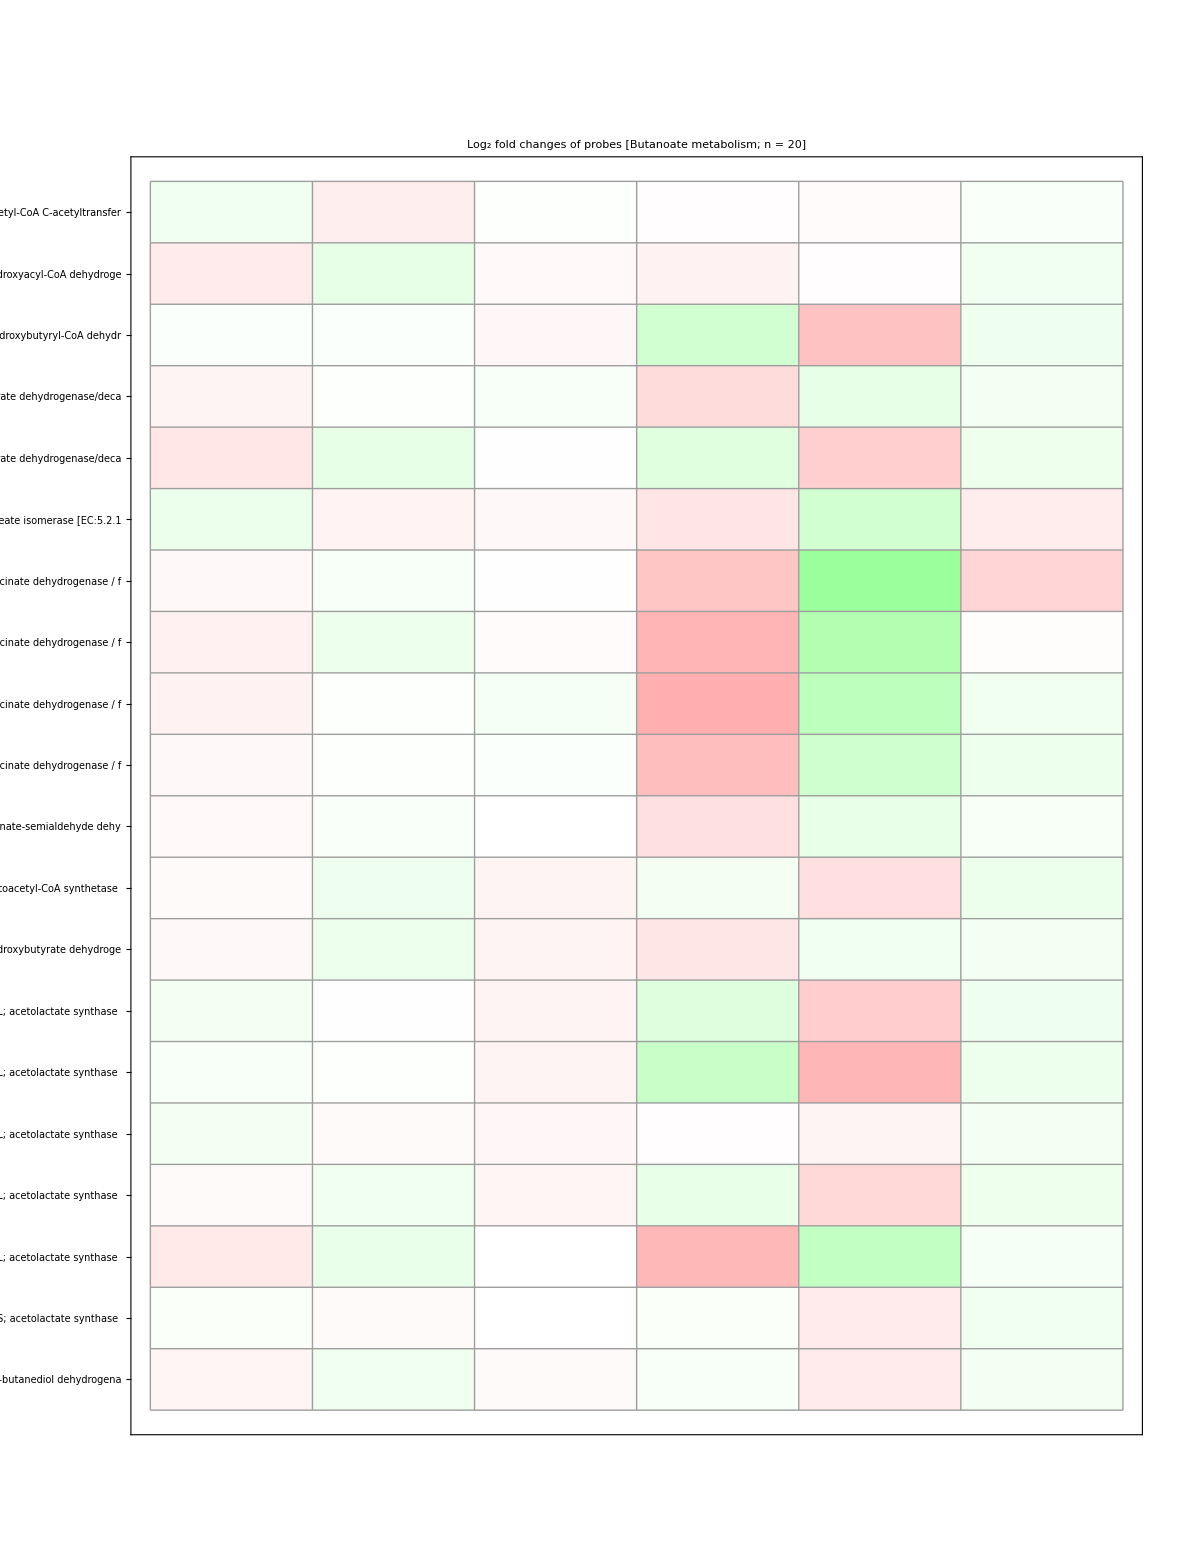

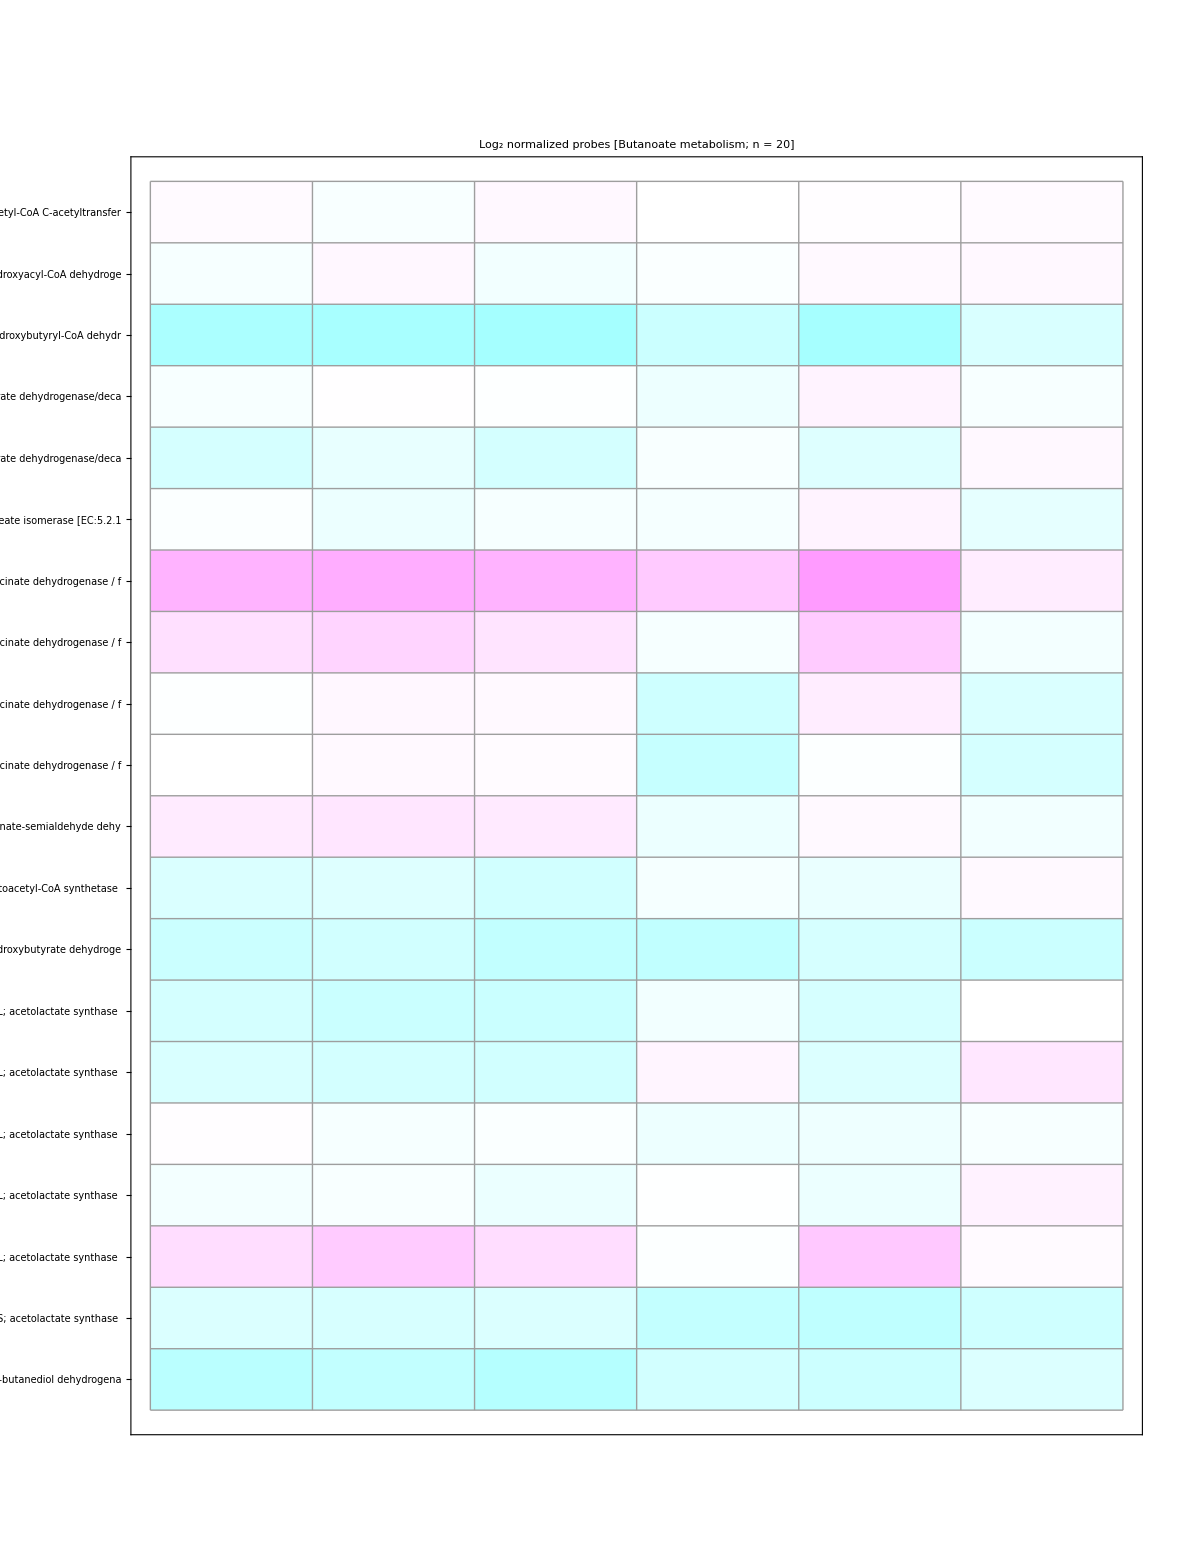

```mathematica
Graphics[{Inset[Show[f[14,1190],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{.2,.7}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[14,1190],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{.2,.7}]]},AspectRatio->Automatic]
```

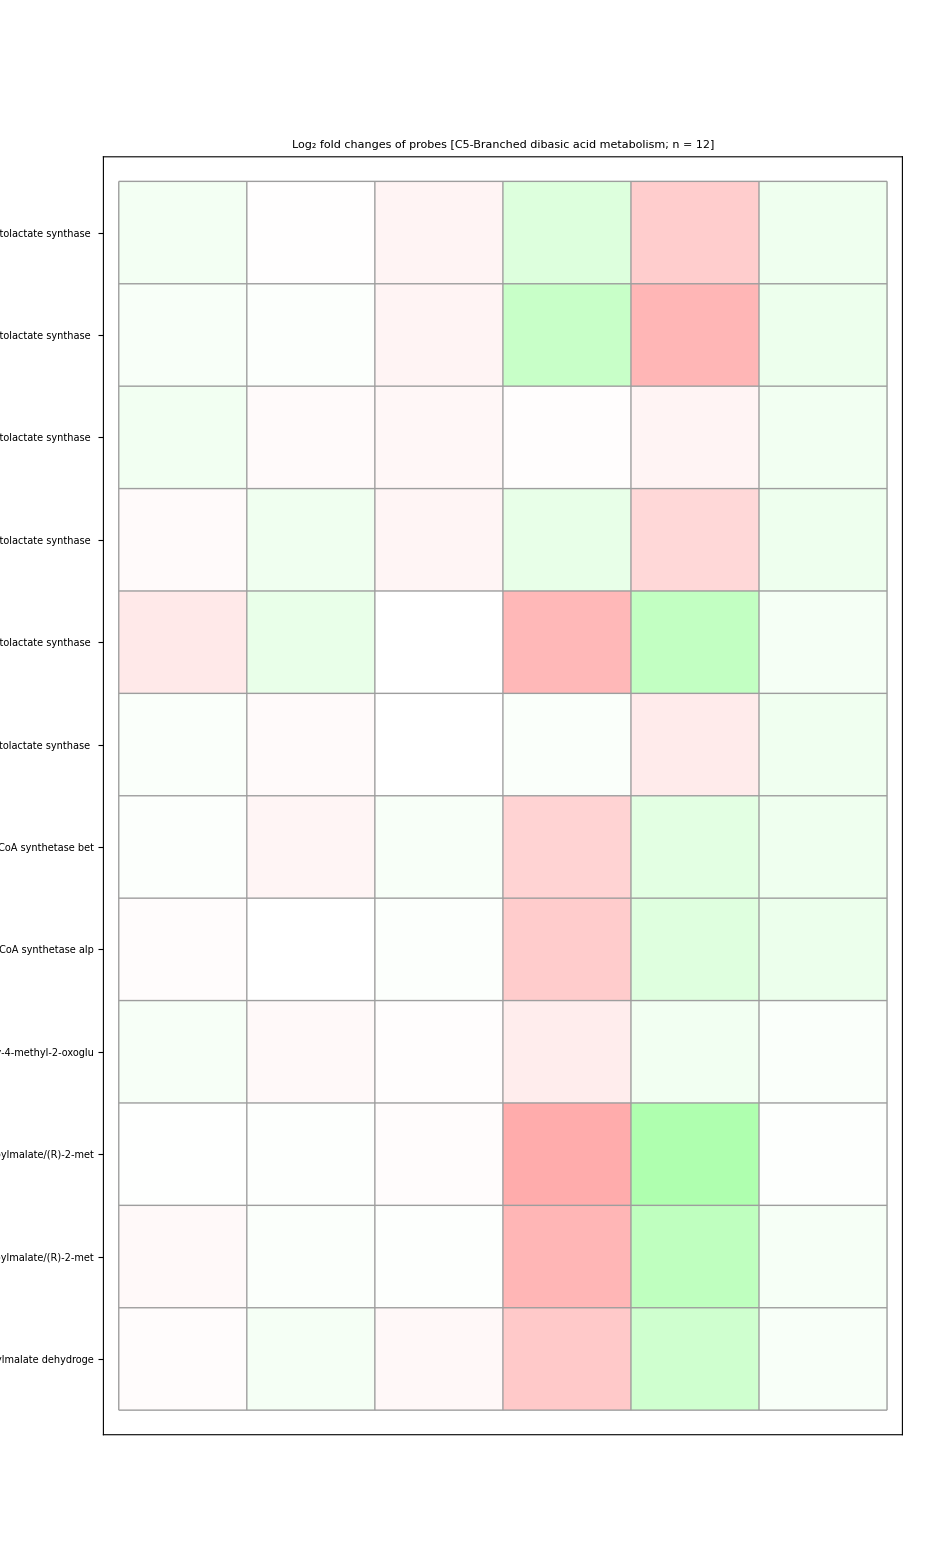

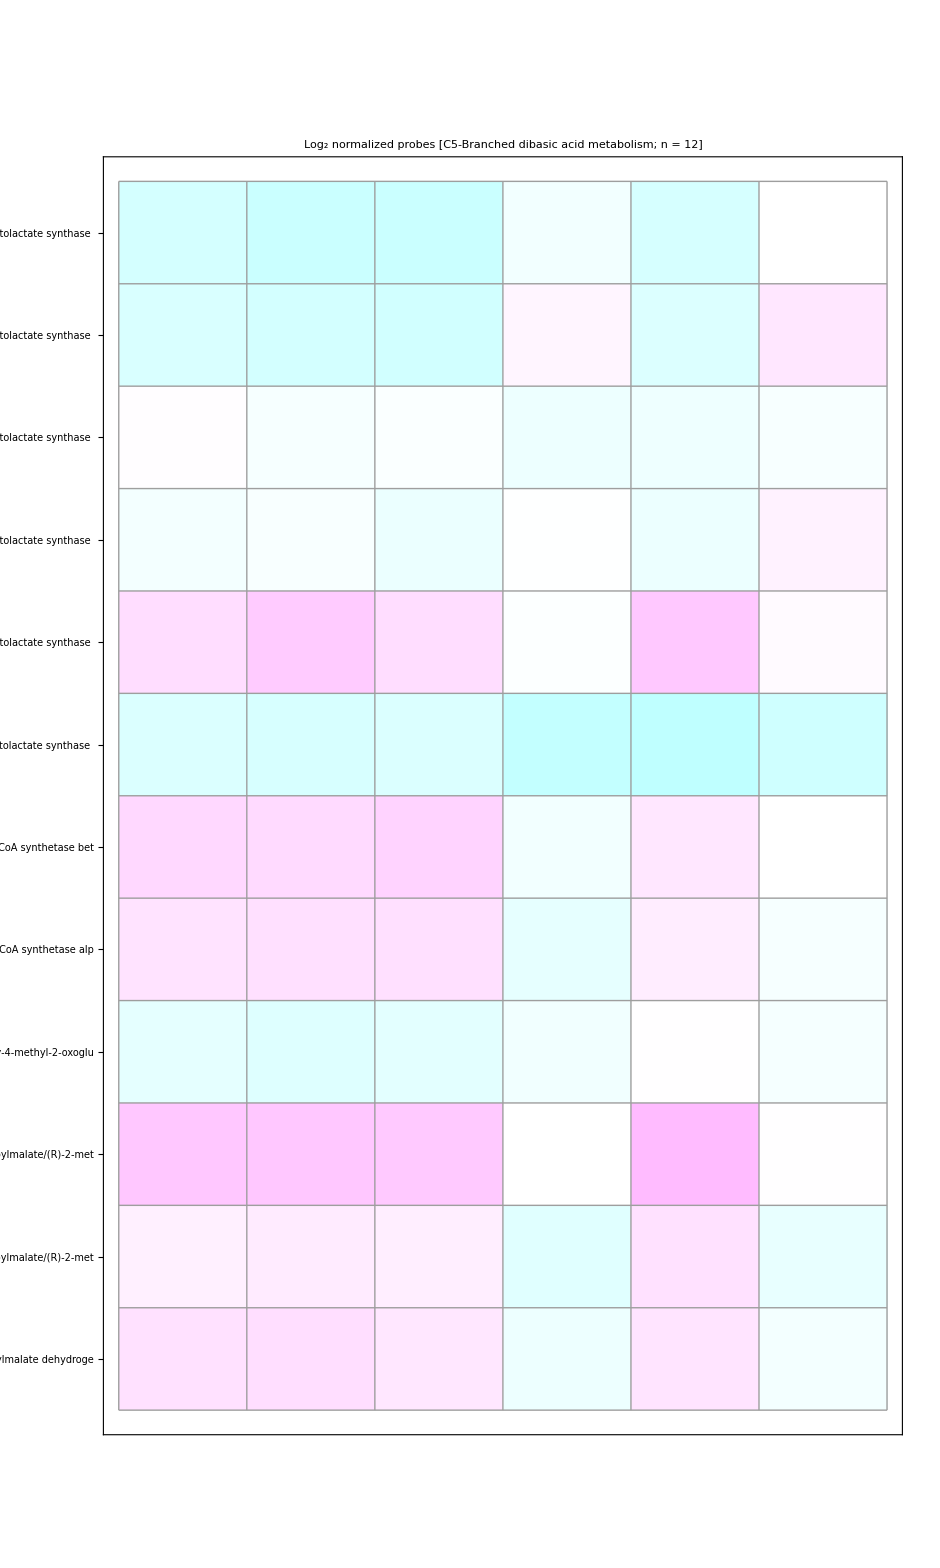

```mathematica
Graphics[{Inset[Show[f[15,940],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{.0,.5}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[15,940],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{0,.5}]]},AspectRatio->Automatic]
```

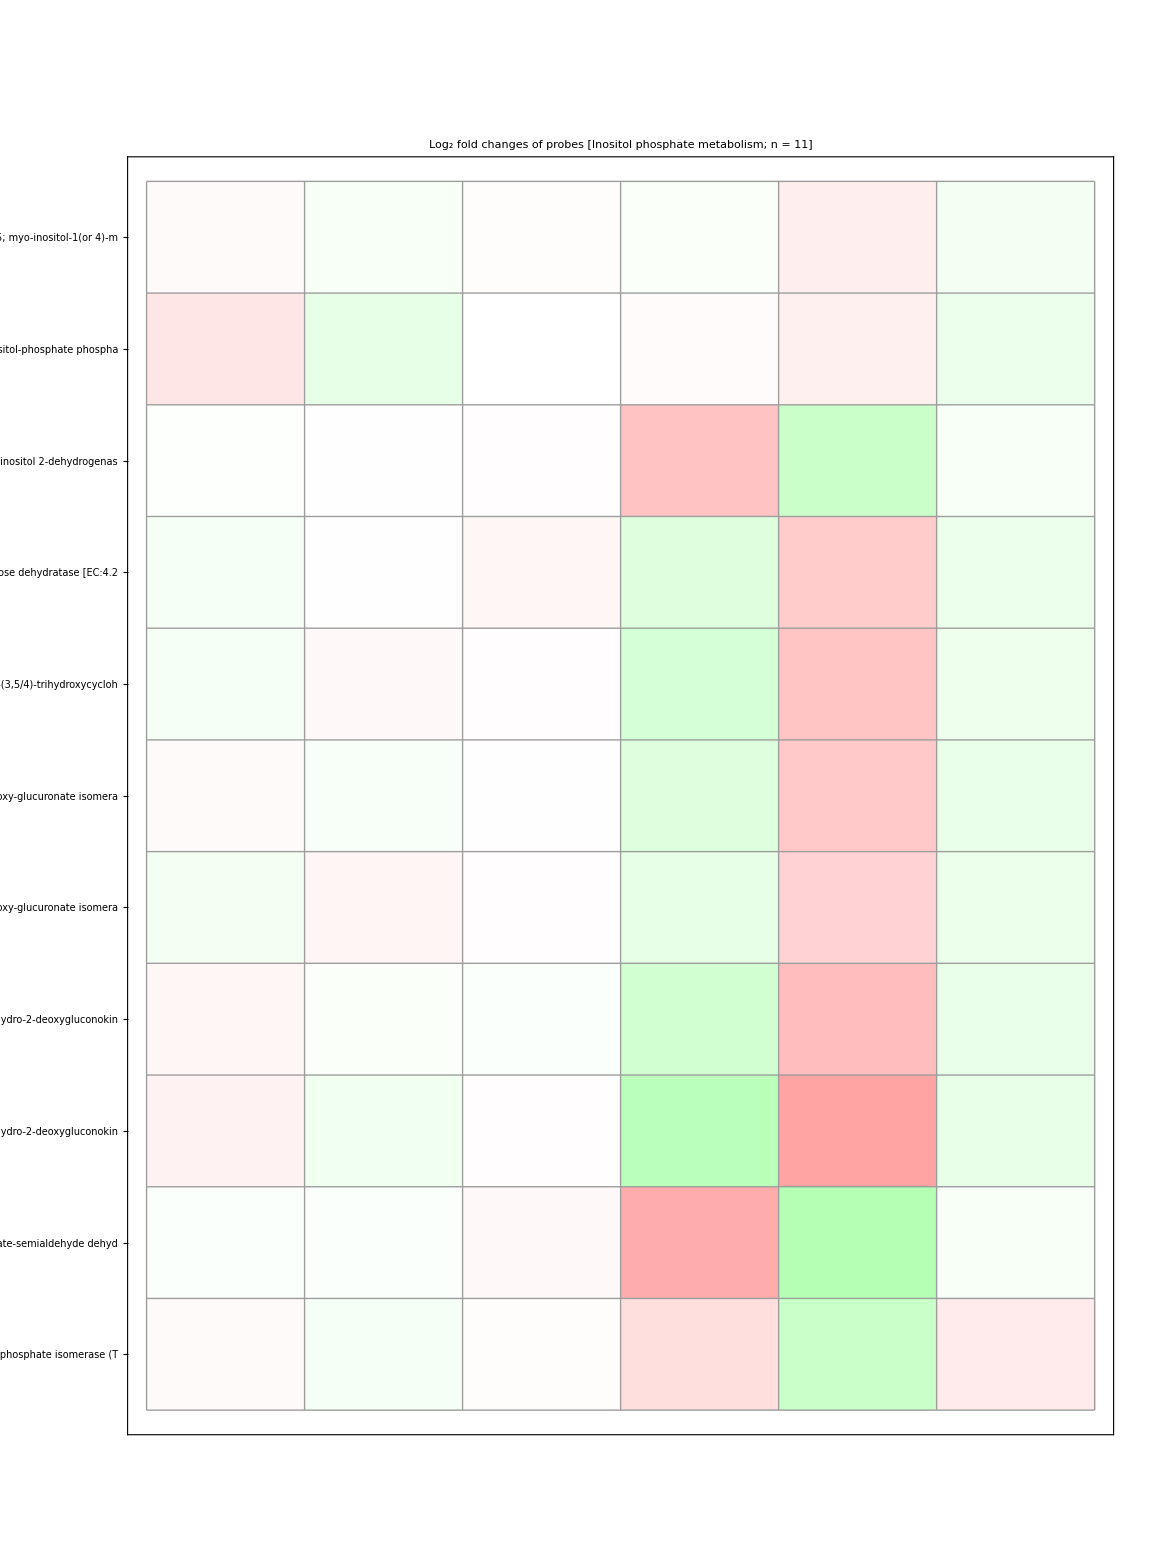

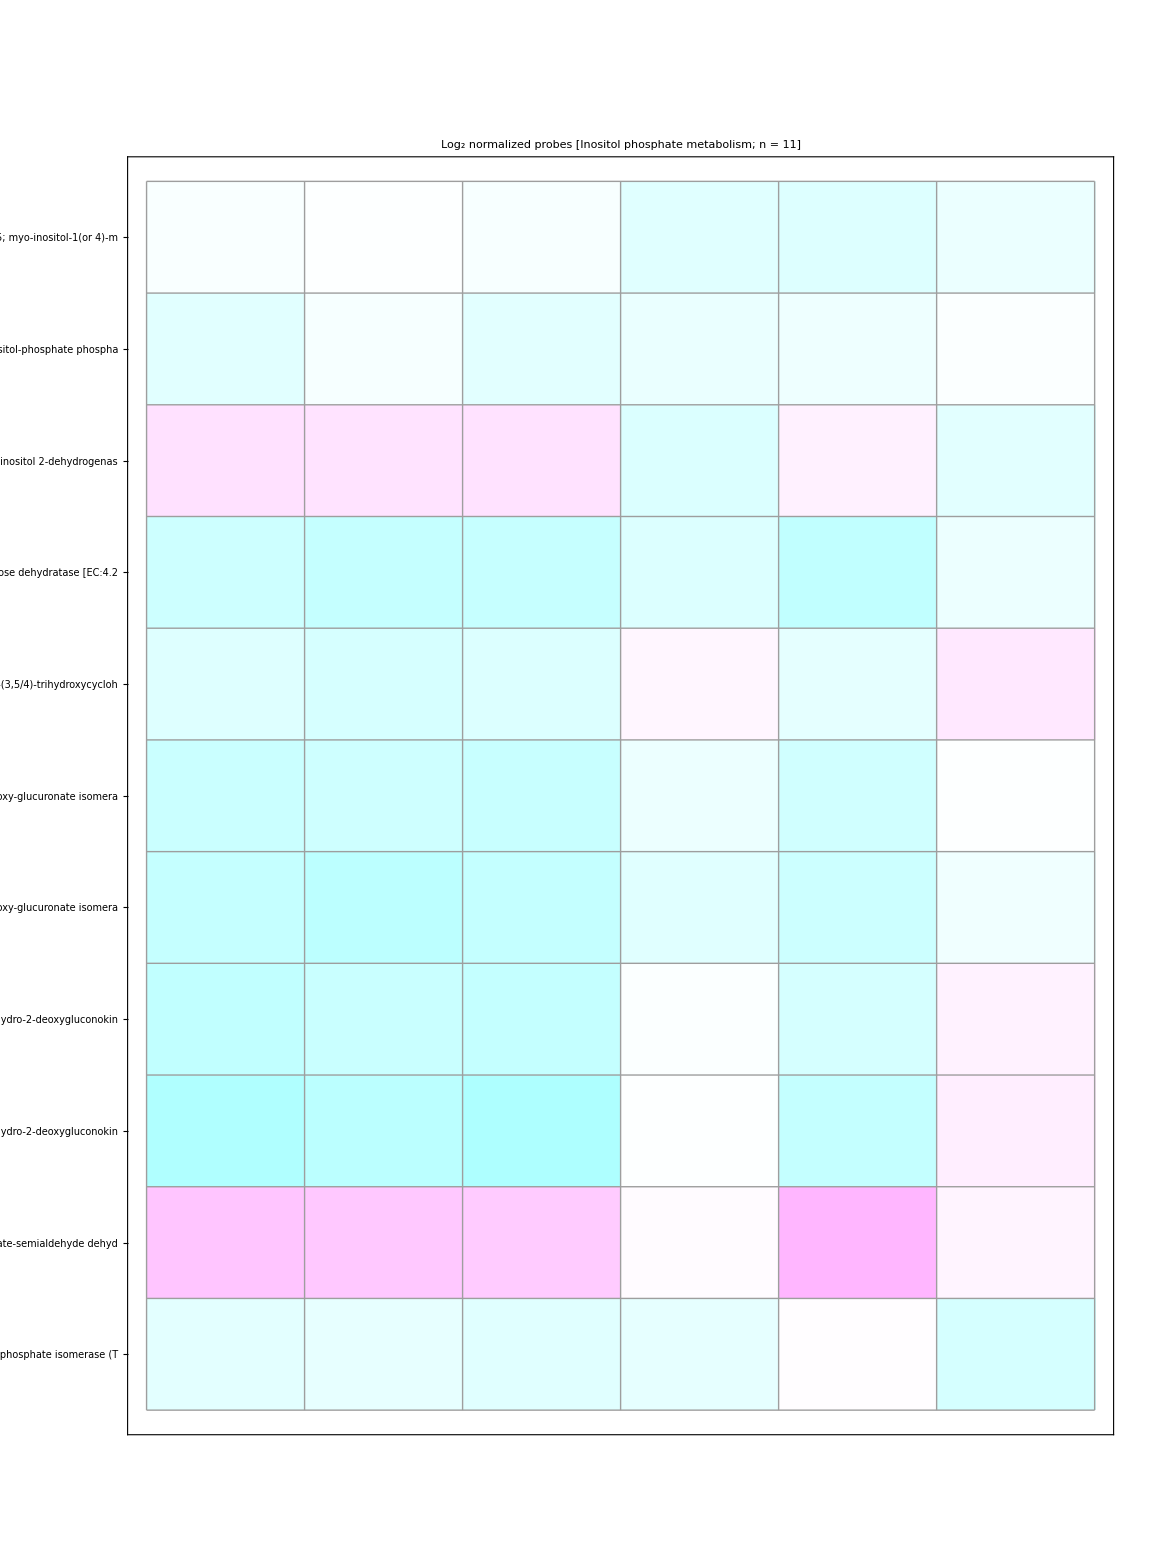

```mathematica
Graphics[{Inset[Show[f[16,1160],AspectRatio->Automatic]],Inset[DensityPlotA,Scaled[{.3,.65}]]},AspectRatio->Automatic]
Graphics[{Inset[Show[g[16,1160],AspectRatio->Automatic]],Inset[DensityPlotB,Scaled[{.3,.65}]]},AspectRatio->Automatic]
```